# Resource allocation to cell envelopes and the scaling of bacterial growth rate

## Derivation of the steady state growth rate

### General equations for evolution of abundances

```mathematica
sphereRadius[vol_]=Solve[vol==4/3 Pi r^3,r][[2]][[All,2]][[1]]
```

((3/π)^(1/3) vol^(1/3))/2^(2/3)

```mathematica
capacities={kn->κn lp,kt->κt lr,kl->κl lp};
```

ODEs describing the evolution of molecular abundances are as follows. All reactions obey Michaelis-Menten kinetics with equal half-saturation constant K_m:

```mathematica
eqBlock=B'[t]==kn Pb[t]-kt R[t](B[t]/V[t])/(Km+B[t]/V[t])-kl Pl[t](B[t]/V[t])/(Km+B[t]/V[t])/.capacities
eqLipid=L'[t]==kl/ls Pl[t](B[t]/V[t])/(Km+B[t]/V[t])-dl L[t]/.capacities
eqRibo=R'[t]==kt/lr R[t](B[t]/V[t])/(Km+B[t]/V[t])ϕr/.capacities
eqProcB=Pb'[t]==kt/lp R[t](B[t]/V[t])/(Km+B[t]/V[t])ϕb-dp Pb[t]/.capacities
eqProcL=Pl'[t]==kt/lp R[t](B[t]/V[t])/(Km+B[t]/V[t])ϕl-dp Pl[t]/.capacities
```

B'[t]==lp κn Pb[t]-(lp κl B[t] Pl[t])/((Km+B[t]/V[t]) V[t])-(lr κt B[t] R[t])/((Km+B[t]/V[t]) V[t])

L'[t]==-dl L[t]+(lp κl B[t] Pl[t])/(ls (Km+B[t]/V[t]) V[t])

R'[t]==(κt ϕr B[t] R[t])/((Km+B[t]/V[t]) V[t])

Pb'[t]==-dp Pb[t]+(lr κt ϕb B[t] R[t])/(lp (Km+B[t]/V[t]) V[t])

Pl'[t]==-dp Pl[t]+(lr κt ϕl B[t] R[t])/(lp (Km+B[t]/V[t]) V[t])

```mathematica
transf={eqBlock,eqRibo,eqProcB,eqProcL,eqLipid}
```

{B'[t]==lp κn Pb[t]-(lp κl B[t] Pl[t])/((Km+B[t]/V[t]) V[t])-(lr κt B[t] R[t])/((Km+B[t]/V[t]) V[t]),R'[t]==(κt ϕr B[t] R[t])/((Km+B[t]/V[t]) V[t]),Pb'[t]==-dp Pb[t]+(lr κt ϕb B[t] R[t])/(lp (Km+B[t]/V[t]) V[t]),Pl'[t]==-dp Pl[t]+(lr κt ϕl B[t] R[t])/(lp (Km+B[t]/V[t]) V[t]),L'[t]==-dl L[t]+(lp κl B[t] Pl[t])/(ls (Km+B[t]/V[t]) V[t])}

```mathematica
adivSS=L[t]
```

L[t]

Taking that all molecular species grow exponentially, we wish to find growth rate in the steady state

```mathematica
sstate=transf/.{B'[t]->B[t]λ,R'[t]->R[t] λ,Pb'[t]->Pb[t]λ,Pl'[t]->Pl[t]λ,L'[t]->L[t] λ };
sstate//MatrixForm
```

(λ B[t]==lp κn Pb[t]-(lp κl B[t] Pl[t])/((Km+B[t]/V[t]) V[t])-(lr κt B[t] R[t])/((Km+B[t]/V[t]) V[t])
λ R[t]==(κt ϕr B[t] R[t])/((Km+B[t]/V[t]) V[t])
λ Pb[t]==-dp Pb[t]+(lr κt ϕb B[t] R[t])/(lp (Km+B[t]/V[t]) V[t])
λ Pl[t]==-dp Pl[t]+(lr κt ϕl B[t] R[t])/(lp (Km+B[t]/V[t]) V[t])
λ L[t]==-dl L[t]+(lp κl B[t] Pl[t])/(ls (Km+B[t]/V[t]) V[t]))

```mathematica
cond={lr>0,lp>0,ϕb>0,ϕr>0,ϕl>0,Km>0,dp>0,ϕr+ϕb+ϕl==1,κn>0,κt>0,κl>0,dr>0,dl>0,γ>0,β>0,ls>0,Π>0};
```

### Analytical solution for λ when K_M>0

```mathematica
transf
```

{B'[t]==lp κn Pb[t]-(lp κl B[t] Pl[t])/((Km+B[t]/V[t]) V[t])-(lr κt B[t] R[t])/((Km+B[t]/V[t]) V[t]),R'[t]==(κt ϕr B[t] R[t])/((Km+B[t]/V[t]) V[t]),Pb'[t]==-dp Pb[t]+(lr κt ϕb B[t] R[t])/(lp (Km+B[t]/V[t]) V[t]),Pl'[t]==-dp Pl[t]+(lr κt ϕl B[t] R[t])/(lp (Km+B[t]/V[t]) V[t]),L'[t]==-dl L[t]+(lp κl B[t] Pl[t])/(ls (Km+B[t]/V[t]) V[t])}

```mathematica
transf[[All,1]]
```

{B'[t],R'[t],Pb'[t],Pl'[t],L'[t]}

```mathematica
V[t]==lp (Pl[t]+Pb[t])+lr R[t]+B[t];
V'[t]==lp (Pl'[t]+Pb'[t])+lr R'[t]+B'[t];
V'[t]==Assuming[cond,transf[[All,2]][[1]]+lr*transf[[All,2]][[2]] +lp*(transf[[All,2]][[3]]+transf[[All,2]][[4]])//FullSimplify]
```

V'[t]==lp ((-dp+κn) Pb[t]+Pl[t] (-dp-(κl B[t])/(B[t]+Km V[t])))

Solving the system, we obtain steady-state values for four variables:

```mathematica
steadyGrowthInflux=lp ((-dp+κn) Pb[t]+Pl[t] (-dp-(κl B[t])/(B[t]+Km V[t])))/V[t]/.capacities;
```

```mathematica
sols=Simplify[Solve[sstate,{B[t],L[t],R[t],Pb[t],Pl[t]}]][[2]][[All,2]];
sols//MatrixForm
```

((Km λ V[t])/(-λ+κt ϕr)
(Km κl λ^3 ϕl V[t])/(ls (dl+λ) (λ-κt ϕr) (κl λ ϕl+κt (dp+λ-κn ϕb) ϕr))
(Km κt λ (dp+λ) ϕr^2 V[t])/(lr (λ-κt ϕr) (κl λ ϕl+κt (dp+λ-κn ϕb) ϕr))
(Km κt λ^2 ϕb ϕr V[t])/(lp (λ-κt ϕr) (κl λ ϕl+κt (dp+λ-κn ϕb) ϕr))
(Km κt λ^2 ϕl ϕr V[t])/(lp (λ-κt ϕr) (κl λ ϕl+κt (dp+λ-κn ϕb) ϕr)))

```mathematica
bSolInt=sols[[1]];
lSolInt=sols[[2]];
rSolInt=sols[[3]];
pbSolInt=sols[[4]];
plSolInt=sols[[5]];
```

```mathematica
aTerm=(λ^2 κt ϕr Km V[t])/((λ-κt ϕr) (κl λ ϕl+κt (dp+λ-κn ϕb) ϕr));
```

```mathematica
Solve[bSolInt==x*aTerm,x]//FullSimplify
Solve[lSolInt==x*aTerm,x]//FullSimplify
Solve[rSolInt==x*aTerm,x]//FullSimplify
Solve[pbSolInt==x*aTerm,x]//FullSimplify
Solve[plSolInt==x*aTerm,x]//FullSimplify
```

{{x→-(dp+λ-κn ϕb)/λ-(κl ϕl)/(κt ϕr)}}

{{x→(κl λ ϕl)/(dl ls κt ϕr+ls κt λ ϕr)}}

{{x→((dp+λ) ϕr)/(lr λ)}}

{{x→ϕb/lp}}

{{x→ϕl/lp}}

Fraction of proteome belonging to a particular sector are equal to the fraction of ribosomes devoted to producing that sector:

```mathematica
Assuming[{ϕb+ϕl+ϕr==1},FullSimplify[(lp plSolInt)/(lr rSolInt+lp plSolInt+lp pbSolInt)]]
```

(λ ϕl)/(λ+dp ϕr)

```mathematica
Assuming[{ϕb+ϕl+ϕr==1},FullSimplify[(lp pbSolInt)/(lr rSolInt+lp plSolInt+lp pbSolInt)]]
```

(λ ϕb)/(λ+dp ϕr)

```mathematica
Assuming[{ϕb+ϕl+ϕr==1},FullSimplify[(lr rSolInt)/(lr rSolInt+lp plSolInt+lp pbSolInt)]]
```

((dp+λ) ϕr)/(λ+dp ϕr)

```mathematica
steadyGrowthInflux==λ/.{Pb[t]->pbSolInt,R[t]->rSolInt, B[t]->bSolInt,Pl[t]->plSolInt}//FullSimplify
```

-(Km λ^2 (κl λ ϕl+κt (-κn ϕb+dp (ϕb+ϕl)) ϕr))/((λ-κt ϕr) (κl λ ϕl+κt (dp+λ-κn ϕb) ϕr))==λ

```mathematica
-Km λ^2 (κl λ ϕl+κt (-κn ϕb+dp (ϕb+ϕl)) ϕr)-λ((λ-κt ϕr) (κl λ ϕl+κt (dp+λ-κn ϕb) ϕr))==0
```

-λ (λ-κt ϕr) (κl λ ϕl+κt (dp+λ-κn ϕb) ϕr)-Km λ^2 (κl λ ϕl+κt (-κn ϕb+dp (ϕb+ϕl)) ϕr)==0

```mathematica
CoefficientList[-λ (λ-κt ϕr) (κl λ ϕl+κt (dp+λ-κn ϕb) ϕr)-Km λ^2 (κl λ ϕl+κt (-κn ϕb+dp (ϕb+ϕl)) ϕr),λ]//FullSimplify
```

{0,κt^2 (dp-κn ϕb) ϕr^2,κt ϕr ((1+Km) κn ϕb+κl ϕl-dp (1+Km (ϕb+ϕl))+κt ϕr),-(1+Km) κl ϕl-κt ϕr}

```mathematica
growthSols=Assuming[cond,Solve[steadyGrowthInflux==λ/.{Pb[t]->pbSolInt,R[t]->rSolInt, B[t]->bSolInt,Pl[t]->plSolInt},λ]//Simplify]
```

{{λ→0},{λ→(κt ϕr (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr+√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr)))))/(2 ((1+Km) κl ϕl+κt ϕr))},{λ→(κt ϕr (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr)))))/(2 ((1+Km) κl ϕl+κt ϕr))}}

```mathematica
Assuming[cond,Assuming[cond,growthSols[[2]]/.dp->0/.ϕr->0//FullSimplify]/.{ϕl->0,ϕb->1}//FullSimplify]
Assuming[cond,Assuming[cond,growthSols[[2]]/.dp->0/.ϕr->1//FullSimplify]/.{ϕl->0,ϕb->0}//FullSimplify]
```

{λ→0}

{λ→κt}

```mathematica
Assuming[cond,Assuming[cond,growthSols[[3]]/.dp->0/.ϕr->0//FullSimplify]/.{ϕl->0,ϕb->1}//FullSimplify]
Assuming[cond,Assuming[cond,growthSols[[3]]/.dp->0/.ϕr->1//FullSimplify]/.{ϕl->0,ϕb->0}//FullSimplify]
```

{λ→0}

{λ→0}

Given that only the third root of cubic polynomial goes to zero when both ϕ_R=0 and ϕ_R=1, this is the biologically relevant solution for the steady-state growth rate:

```mathematica
ssLambda=growthSols[[3]][[All,2]][[1]]
```

(κt ϕr (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr)))))/(2 ((1+Km) κl ϕl+κt ϕr))

```mathematica
explicitSols=sols/.λ->ssLambda;
```

```mathematica
bSolExp=explicitSols[[1]];
lSolExp=explicitSols[[2]];
rSolExp=explicitSols[[3]];
pbSolExp=explicitSols[[4]];
plSolExp=explicitSols[[5]];
```

```mathematica
explicitVol=v/γ;
explicitSurf=adivSS/β/.{L[t]->lSolExp}/.V[t]->v//Simplify;
```

```mathematica
Assuming[{Km>0,1>ϕb>0,1>ϕr>0},Limit[ssLambda/.{ϕl->0,ϕb->1-ϕr},κn->Infinity]//Simplify]/.ϕr->1
Assuming[{Km>0,1>ϕb>0,1>ϕr>0},Limit[ssLambda/.{ϕl->0,ϕb->1-ϕr},κt->Infinity]//Simplify]/.ϕr->0
```

κt/(1+Km)

-dp+κn

### Scaling of λ_max with Ṽ

```mathematica
frameTicksArray={{{#,Superscript[10,Log10@#]}&/@Table[10^i,{i,-2,1}],Automatic},{{#,Superscript[10,Log10@#]}&/@Table[10^i,{i,-2,5}],Automatic}};
```

```mathematica
cellGeometryConstraint=explicitSurf/explicitVol==3/sphereRadius[explicitVol];
```

However, there is an upper limit on how many P molecs because they reside in the membrane

```mathematica
aaPerVol=325*3*10^6 (* μm^3 -- Milo and Phillips 2016 *);
lipPerSurf=2*10^6 (* μm^2 -- Langmuir 1917, Phillips 2019 *);
```

```mathematica
κlPar=288.1596;
κtPar=2.589108;
kmPar=10^-3;
dpPar=0.1438542;
dlPar=0.147;
lrPar=7336;
lpPar=325;
```

```mathematica
NOptimize[numSys_,n_]:=Module[{i,j,bestSolPosition,possibleSols},
possibleSols=Table[{},{i,1,n}];

Monitor[Do[
possibleSols[[j]]=NMaximize[Rationalize[numSys],{ϕl,ϕb,ϕr},Method->{"NelderMead","RandomSeed"->j,"ContractRatio"->0.85},MaxIterations->2000],
{j,Length[possibleSols]}]
,j];
bestSolPosition=FirstPosition[possibleSols[[All,1]],Max[possibleSols[[All,1]]]][[1]];
possibleSols[[bestSolPosition]]
]
```

```mathematica
κnEmpirical={1.52728,3.228333,4.4852,6.281437,7.933559,12.144675};
minM=3+3;maxM=10+3;
mDivArray=Table[10^i,{i,minM,maxM,0.25}]//Reverse;
partitionArray=Table[Table[{0,0,0,0},{i,1,Length[mDivArray]}],{k,1,Length[κnEmpirical]}];
maxGrowthArray=phiRarray=phiLarray=violationArray=Table[Table[{0,0},{i,1,Length[mDivArray]}],{k,1,Length[κnEmpirical]}];
```

```mathematica
params={γ->aaPerVol,β->lipPerSurf,lp->325,lr->7336,ls->314,κt->κtPar,κl->κlPar,Km->kmPar,dp->dpPar,dl->dlPar};
Monitor[
Do[
Do[
mainSys={ssLambda,cellGeometryConstraint}/.params/.v->mDivArray[[i]]/.κn->κnEmpirical[[k]];

numSys={mainSys[[1]],{mainSys[[2]],ϕr+ϕl+ϕb==1,1≥ϕr≥0,1≥ϕl≥0,1≥ϕb≥0}};
numSol=NOptimize[numSys,20];

maxGrowthArray[[k,i,2]]=numSol[[1]];
partitionArray[[k,i,1]]=numSol[[2]][[All,2]][[1]] (* Subscript[ϕ, l,opt] *);
partitionArray[[k,i,2]]=numSol[[2]][[All,2]][[2]] (* Subscript[ϕ, b,opt] *);
partitionArray[[k,i,3]]=numSol[[2]][[All,2]][[3]] (* Subscript[ϕ, r,opt] *);

maxGrowthArray[[k,i,1]]=(explicitSurf/explicitVol)/.params/.v->mDivArray[[i]]/.κn->κnEmpirical[[k]]/.{ϕl->numSol[[2]][[All,2]][[1]],ϕb->numSol[[2]][[All,2]][[2]],ϕr->numSol[[2]][[All,2]][[3]]};(* SA:V *)

violationArray[[k,i,2]]=(explicitSurf/explicitVol)/(3/sphereRadius[explicitVol])/.params/.v->mDivArray[[i]]/.κn->κnEmpirical[[k]]/.{ϕl->numSol[[2]][[All,2]][[1]],ϕb->numSol[[2]][[All,2]][[2]],ϕr->numSol[[2]][[All,2]][[3]]};
violationArray[[k,i,1]]=maxGrowthArray[[k,i,1]];
partitionArray[[k,i,4]]=maxGrowthArray[[k,i,1]] (* V *);,
{i,Length[mDivArray]}];,
{k,Length[κnEmpirical]}],
{k,i,mDivArray[[i]],κnEmpirical[[k]]}]
```

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {2.2258+(1.15832 ϕl ϕr (0.143854-1.52866 ϕb-288.159 ϕl-(647277 ϕr)/250000+√(Power[«2»]+Times[«3»]))^3)/((0.143854-1.52866 ϕb+288.736 ϕl+(647277 ϕr)/250000+√(Power[«2»]+Times[«3»])) (84.8036 ϕl+«6») (-41.5359 ϕl+440.582 ϕb ϕl-83035.9 ϕl^2-0.372454 ϕr+3.95071 ϕb ϕr-1492.15 ϕl ϕr-6.70348 ϕr^2+(720399 ϕl √Plus[«2»])/2500+(647277 ϕr √Plus[«2»])/250000))==0,-ϕb≤0}.

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {2.69662+(1.15832 ϕl ϕr (0.143854-1.52866 ϕb-288.159 ϕl-(647277 ϕr)/250000+√(Power[«2»]+Times[«3»]))^3)/((0.143854-1.52866 ϕb+288.736 ϕl+(647277 ϕr)/250000+√(Power[«2»]+Times[«3»])) (84.8036 ϕl+«6») (-41.5359 ϕl+440.582 ϕb ϕl-83035.9 ϕl^2-0.372454 ϕr+3.95071 ϕb ϕr-1492.15 ϕl ϕr-6.70348 ϕr^2+(720399 ϕl √Plus[«2»])/2500+(647277 ϕr √Plus[«2»])/250000))==0,-ϕb≤0}.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NMaximize::nnum: The function value Indeterminate is not a number at {ϕb,ϕl,ϕr} = {0.85366,0.14634,0.}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NMaximize::nnum: The function value Indeterminate is not a number at {ϕb,ϕl,ϕr} = {0.780855,0.219145,0.}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {15.1642+(1.15832 ϕl ϕr (0.143854-1.52866 ϕb-288.159 ϕl-(647277 ϕr)/250000+√(Power[«2»]+Times[«3»]))^3)/((0.143854-1.52866 ϕb+288.736 ϕl+(647277 ϕr)/250000+√(Power[«2»]+Times[«3»])) (84.8036 ϕl+«20» ϕr+«5») (-41.5359 ϕl+440.582 ϕb ϕl-83035.9 ϕl^2-0.372454 ϕr+3.95071 ϕb ϕr-1492.15 ϕl ϕr-6.70348 ϕr^2+(720399 ϕl √Plus[«2»])/2500+(647277 ϕr √Plus[«2»])/250000))==0}.

General::stop: Further output of NMaximize::nosat will be suppressed during this calculation.

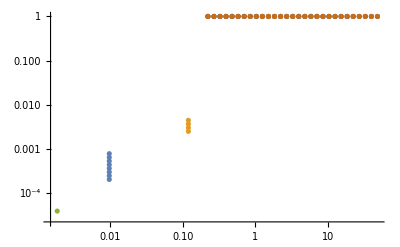

```mathematica
ListPlot[violationArray,PlotRange->Full,ScalingFunctions->{"Log10","Log10"},PlotRange->All]
```

```mathematica
numerical=ListPlot[maxGrowthArray,Frame->True,PlotTheme->"Scientific",FrameLabel->{"S/V (μm^-1)","Max growth rate (h^-1)"},Joined->False,ScalingFunctions->{"Log10","Log10"},PlotLegends->False,ImageSize->Large,FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},PlotMarkers->{"□",30}];
```

```mathematica
lambdaAnalytic[κn_,κt_,κl_,dp_,dl_,ls_,β_,γ_,Π_]=(κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π)/(κl (κn+κt)+ϵ (κl+κn) (dp+κt) Π)/.ϵ->ls β/γ;
phiLAnalytic[κn_,κt_,κl_,dp_,dl_,ls_,β_,γ_,Π_]=(ϵ (dp+κt) (dl κn+(dl-dp+κn) κt) Π)/(κl κt (κn+κt)+ϵ (κl+κn) κt (dp+κt) Π)/.ϵ->ls β/γ;
phiRAnalytic[κn_,κt_,κl_,dp_,dl_,ls_,β_,γ_,Π_]=(κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π)/(κl κt (κn+κt)+ϵ (κl+κn) κt (dp+κt) Π)/.ϵ->ls β/γ;
```

```mathematica
analytic=Plot[{
lambdaAnalytic[κnEmpirical[[1]],κtPar,κlPar,dpPar,dlPar,314,lipPerSurf,aaPerVol,Π],
lambdaAnalytic[κnEmpirical[[2]],κtPar,κlPar,dpPar,dlPar,314,lipPerSurf,aaPerVol,Π],
lambdaAnalytic[κnEmpirical[[3]],κtPar,κlPar,dpPar,dlPar,314,lipPerSurf,aaPerVol,Π],
lambdaAnalytic[κnEmpirical[[4]],κtPar,κlPar,dpPar,dlPar,314,lipPerSurf,aaPerVol,Π],
lambdaAnalytic[κnEmpirical[[5]],κtPar,κlPar,dpPar,dlPar,314,lipPerSurf,aaPerVol,Π],
lambdaAnalytic[κnEmpirical[[6]],κtPar,κlPar,dpPar,dlPar,314,lipPerSurf,aaPerVol,Π]
},{Π,0.2,50},Frame->True,PlotTheme->"Scientific",FrameLabel->{"S/V (μm^-1)","λ_max (h^-1)"},PlotLegends->False,ImageSize->Large,PlotStyle->Thickness[0.0075],ScalingFunctions->{"Log10","Log10"},FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold}];
```

```mathematica
growthPlotNumAn=Show[analytic,numerical];
```

```mathematica
Do[
phiRarray[[k,i,1]]=phiLarray[[k,i,1]]=maxGrowthArray[[k,i,1]];
phiRarray[[k,i,2]]=((dp+λ) ϕr)/(λ+dp ϕr)/.params/.{ϕr->partitionArray[[k,i,3]],λ->partitionArray[[k,i,4]]};
phiLarray[[k,i,2]]=(λ ϕl)/(λ+dp ϕr)/.params/.{ϕr->partitionArray[[k,i,3]],ϕl->partitionArray[[k,i,1]],λ->partitionArray[[k,i,4]]};,
{i,1,Length[mDivArray]},{k,1,Length[κnEmpirical]}
];
```

```mathematica
analyticPhiL=Plot[{
phiLAnalytic[κnEmpirical[[1]],κtPar,κlPar,dpPar,dlPar,314,lipPerSurf,aaPerVol,Π],
phiLAnalytic[κnEmpirical[[2]],κtPar,κlPar,dpPar,dlPar,314,lipPerSurf,aaPerVol,Π],
phiLAnalytic[κnEmpirical[[3]],κtPar,κlPar,dpPar,dlPar,314,lipPerSurf,aaPerVol,Π],
phiLAnalytic[κnEmpirical[[4]],κtPar,κlPar,dpPar,dlPar,314,lipPerSurf,aaPerVol,Π],
phiLAnalytic[κnEmpirical[[5]],κtPar,κlPar,dpPar,dlPar,314,lipPerSurf,aaPerVol,Π],
phiLAnalytic[κnEmpirical[[6]],κtPar,κlPar,dpPar,dlPar,314,lipPerSurf,aaPerVol,Π]
},{Π,0.2,50},Frame->True,PlotTheme->"Scientific",FrameLabel->{"S/V (μm^-1)","λ_max (h^-1)"},PlotLegends->False,ImageSize->Large,PlotStyle->Directive[{Dashed,Thickness[0.0075]}],ScalingFunctions->{"Log10","Log10"},FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold}];
```

```mathematica
analyticPhiR=Plot[{
phiRAnalytic[κnEmpirical[[1]],κtPar,κlPar,dpPar,dlPar,314,lipPerSurf,aaPerVol,Π],
phiRAnalytic[κnEmpirical[[2]],κtPar,κlPar,dpPar,dlPar,314,lipPerSurf,aaPerVol,Π],
phiRAnalytic[κnEmpirical[[3]],κtPar,κlPar,dpPar,dlPar,314,lipPerSurf,aaPerVol,Π],
phiRAnalytic[κnEmpirical[[4]],κtPar,κlPar,dpPar,dlPar,314,lipPerSurf,aaPerVol,Π],
phiRAnalytic[κnEmpirical[[5]],κtPar,κlPar,dpPar,dlPar,314,lipPerSurf,aaPerVol,Π],
phiRAnalytic[κnEmpirical[[6]],κtPar,κlPar,dpPar,dlPar,314,lipPerSurf,aaPerVol,Π]
},{Π,0.2,50},Frame->True,PlotTheme->"Scientific",FrameLabel->{"S/V (μm^-1)","λ_max (h^-1)"},PlotLegends->False,ImageSize->Large,PlotStyle->Thickness[0.0075],ScalingFunctions->{"Log10","Log10"},FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold}];
```

```mathematica
numericalPhiR=ListPlot[phiRarray,Frame->True,PlotTheme->"Scientific",FrameLabel->{"S/V (μm^-1)","Proteome mass fraction, Φ"},Joined->False,PlotLegends->False,ScalingFunctions->{"Log10","Log10"},ImageSize->Large,FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},PlotStyle->Directive[{PointSize[0.025]}],PlotRange->{{0.15,45},{0.00025,1}}];
numericalPhiL=ListPlot[phiLarray,Frame->True,PlotTheme->"Scientific",FrameLabel->{"S/V (μm^-1)","Proteome mass fraction, Φ"},Joined->False,PlotLegends->False,PlotMarkers->{"◦",30},ScalingFunctions->{"Log10","Log10"},ImageSize->Large,FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},PlotStyle->Directive[{PointSize[0.025]}],PlotRange->{{0.15,45},{0.00025,1}}];
phiPlotNumAn=Show[numericalPhiR,numericalPhiL,analyticPhiR,analyticPhiL];
```

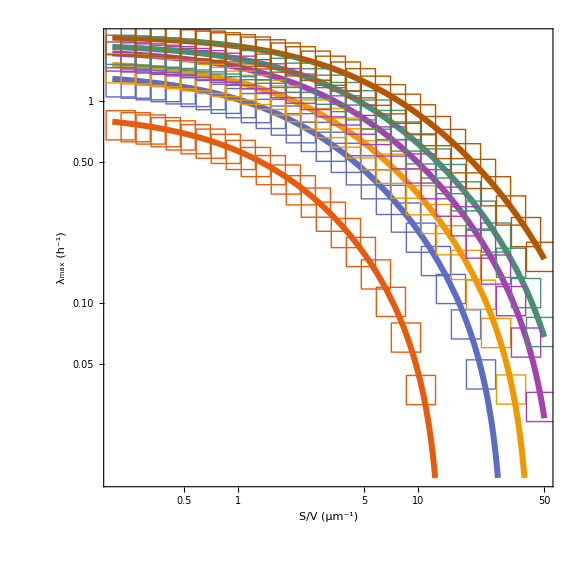

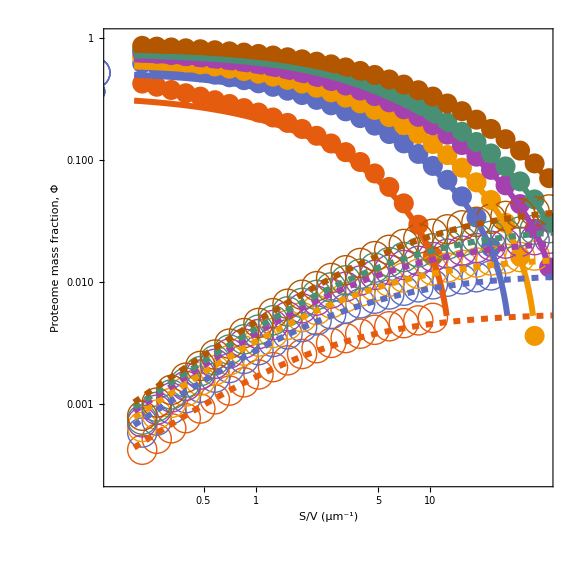

```mathematica
growthPlotNumAn
phiPlotNumAn
```

```mathematica
kmArray={10^-2,10^-1,1};
minM=3+3;maxM=10+3;
mDivArray=Table[10^i,{i,minM,maxM,0.5}]//Reverse;
partitionArray=Table[Table[{0,0,0,0},{i,1,Length[mDivArray]}],{k,1,Length[kmArray]}];
maxGrowthArray=phiRarray=phiLarray=violationArray=Table[Table[{0,0},{i,1,Length[mDivArray]}],{k,1,Length[kmArray]}];
```

```mathematica
params={γ->aaPerVol,β->lipPerSurf,lp->325,lr->7336,ls->314,κt->κtPar,κl->κlPar,κn->κnEmpirical[[6]],dp->dpPar,dl->dlPar};
Monitor[
Do[
Do[
mainSys={ssLambda,cellGeometryConstraint}/.params/.v->mDivArray[[i]]/.Km->kmArray[[k]];

numSys={mainSys[[1]],{mainSys[[2]],ϕr+ϕl+ϕb==1,1≥ϕr≥0,1≥ϕl≥0,1≥ϕb≥0}};
numSol=NOptimize[numSys,20];

maxGrowthArray[[k,i,2]]=numSol[[1]];
partitionArray[[k,i,1]]=numSol[[2]][[All,2]][[1]] (* Subscript[ϕ, l,opt] *);
partitionArray[[k,i,2]]=numSol[[2]][[All,2]][[2]] (* Subscript[ϕ, b,opt] *);
partitionArray[[k,i,3]]=numSol[[2]][[All,2]][[3]] (* Subscript[ϕ, r,opt] *);

maxGrowthArray[[k,i,1]]=(explicitSurf/explicitVol)/.params/.v->mDivArray[[i]]/.Km->kmArray[[k]]/.{ϕl->numSol[[2]][[All,2]][[1]],ϕb->numSol[[2]][[All,2]][[2]],ϕr->numSol[[2]][[All,2]][[3]]};(* SA:V *)

violationArray[[k,i,2]]=(explicitSurf/explicitVol)/(3/sphereRadius[explicitVol])/.params/.v->mDivArray[[i]]/.Km->kmArray[[k]]/.{ϕl->numSol[[2]][[All,2]][[1]],ϕb->numSol[[2]][[All,2]][[2]],ϕr->numSol[[2]][[All,2]][[3]]};
violationArray[[k,i,1]]=maxGrowthArray[[k,i,1]];
partitionArray[[k,i,4]]=maxGrowthArray[[k,i,1]] (* V *);,
{i,Length[mDivArray]}];,
{k,Length[kmArray]}],
{k,i,mDivArray[[i]],kmArray[[k]]}]
```

```mathematica
largeKmAnalyticPlot=Plot[{
lambdaAnalytic[κnEmpirical[[6]],κtPar,κlPar,dpPar,dlPar,314,lipPerSurf,aaPerVol,Π]
},{Π,0.2,50},Frame->True,PlotTheme->"Scientific",FrameLabel->{"S/V (μm^-1)","λ_max (h^-1)"},PlotLegends->False,ImageSize->Large,PlotStyle->{Darker[Red],Thickness[0.0075]},ScalingFunctions->{"Log10","Log10"},FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold}];
```

```mathematica
largeKmNumericPlot=ListPlot[maxGrowthArray,Frame->True,PlotTheme->"Scientific",FrameLabel->{"S/V (μm^-1)","Max growth rate (h^-1)"},Joined->False,ScalingFunctions->{"Log10","Log10"},ImageSize->Large,FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},PlotMarkers->{"□",30},PlotRange->All,PlotStyle->{Darker[Red],Red,Lighter[Red]},PlotLegends->{"K_M=0.01","K_M=0.1","K_M=1"}];
```

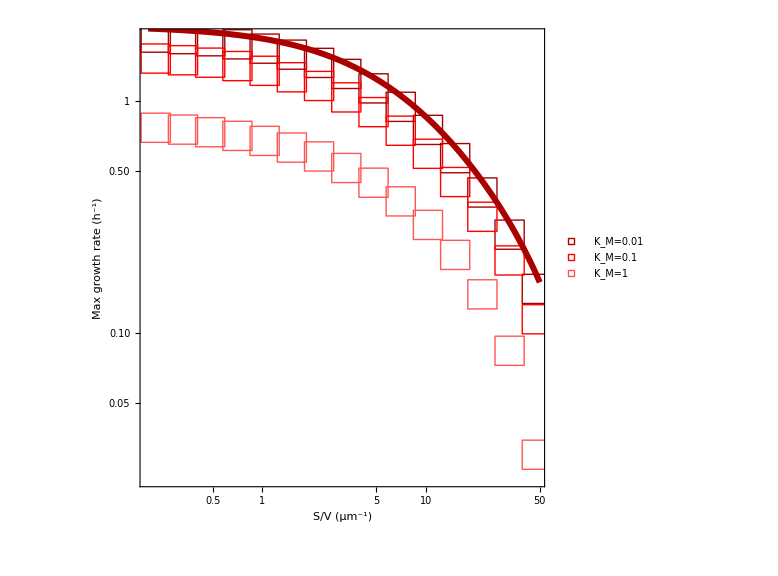

```mathematica
Show[largeKmNumericPlot,largeKmAnalyticPlot]
```

```mathematica
paramsTest=.;
paramsTest={γ->aaPerVol,β->lipPerSurf,lp->325,lr->7336,ls->314,κt->κtPar,κl->0.015*κlPar,Km->0.1,dp->0,dl->0,κn->5,v->3*10^9};
mainSys={ssLambda,cellGeometryConstraint}/.paramsTest/.v->3*10^9;
numSys={mainSys[[1]],{mainSys[[2]],1≥ϕr≥0,1≥ϕl≥0,1≥ϕb≥0,ϕr+ϕb+ϕl==1}};
numSol=NMaximize[Rationalize[numSys],{ϕl,ϕr,ϕb},MaxIterations->5000][[2]][[1;;2]][[All,2]]
```

{0.403622,0.246954}

```mathematica
solutionSpaceNoDeg=ContourPlot[(Log10[ssLambda]/.paramsTest/.ϕb->1-ϕr-ϕl),{ϕl,0,1},{ϕr,0,1},PlotLegends->Automatic,Frame->True,Contours->20,PlotPoints->50,ContourStyle->Directive[White,Dashed,Thick],FrameLabel->{"ϕ_l","ϕ_r"},ImageSize->Medium,
FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],PlotRange->{{0,1},{0,1}},AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},Epilog->{
{PointSize[Large],{Gray,Point[{0.6,0.2}]}},
{PointSize[Large],{Gray,Point[{0.2,0.6}]}},
{PointSize[Large],{Gray,Point[{0.45,0.325}]}},
{PointSize[Large],{Black,Point[numSol]}}
}
];
```

```mathematica
xx=((explicitSurf/explicitVol)/(3/sphereRadius[explicitVol])==1/.paramsTest/.ϕb->1-ϕr-ϕl);
solutionSpaceGeom=ContourPlot[xx//Evaluate,{ϕl,0,0.95},{ϕr,0,0.95},PlotLegends->Automatic,Frame->True,PlotPoints->50,FrameLabel->{"ϕ_l","ϕ_r"},ImageSize->Medium,
FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],PlotRange->{{0,1},{0,1}},AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},ContourStyle->Darker[Red]];
```

```mathematica
noSolution=RegionPlot[(ssLambda<0/.paramsTest/.ϕb->1-ϕr-ϕl),{ϕl,0,1},{ϕr,0,1},PlotLegends->Automatic,Frame->True,ImageSize->Medium,
FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],PlotRange->{{0,1},{0,1}},AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},PlotStyle->White,BoundaryStyle->Darker[Gray]];
```

```mathematica
Show[solutionSpaceNoDeg,solutionSpaceGeom,noSolution]
```

-Graphics-

```mathematica
stadiumEq[r_,a_]=((x-a-Sqrt[r^2-y^2])(x+a+Sqrt[r^2-y^2])(y-r)(y+r));
```

```mathematica
plotStadium[xLow_,xHigh_,yLow_,yHigh_,ϕl_,ϕr_,αx_,βx_,αy_,βy_,r_,a_]:=Module[{phiBbound,phiLbound},
phiBbound=xLow+(1-ϕl-ϕr)*(-xLow+xHigh);
phiLbound=phiBbound+ϕl*(-xLow+xHigh);
envBoundary=ContourPlot[stadiumEq[r,a]==10^-1,{x,αx xLow,βx xHigh},{y,αy yLow,βy yHigh},ContourStyle->Directive[Lighter[Black],Thickness[0.02]],Frame->False];
volContent=RegionPlot[{x<phiBbound&&stadiumEq[4,4]>10^-1,phiLbound>x>phiBbound&&stadiumEq[4,4]>10^-1,x>phiLbound&&stadiumEq[4,4]>10^-1},{x,-10,10},{y,-10,10},Frame->False,
Epilog->{
Text[Style["Φ_B",10,Bold,Italic],{(xLow+phiBbound)/2.25,0}],
Text[Style["Φ_L",10,Bold,Italic],{(phiBbound+phiLbound)/2,0}],
Text[Style["Φ_R",10,Bold,Italic],{(xHigh+phiLbound)/2.1,0}]
}]//Quiet;
Show[volContent,envBoundary]
]
```

```mathematica
plotStadiumSVfixed[xLow_,xHigh_,yLow_,yHigh_,ϕl_,ϕr_,αx_,βx_,αy_,βy_,r_,a_]:=Module[{phiBbound,phiLbound},
phiBbound=xLow+(1-ϕl-ϕr)*(-xLow+xHigh);
phiLbound=phiBbound+ϕl*(-xLow+xHigh);
envBoundary=ContourPlot[stadiumEq[r,a]==10^-1,{x,αx xLow,βx xHigh},{y,αy yLow,βy yHigh},ContourStyle->Directive[Lighter[Black],Thickness[0.02]],Frame->False];
volContent=RegionPlot[{x<phiBbound&&stadiumEq[r,a]>10^-1,phiLbound>x>phiBbound&&stadiumEq[r,a]>10^-1,x>phiLbound&&stadiumEq[r,a]>10^-1},{x,-10,10},{y,-10,10},Frame->False,
Epilog->{
Text[Style["Φ_B",10,Bold,Italic],{(xLow+phiBbound)/2.25,0}],
Text[Style["Φ_L",10,Bold,Italic],{(phiBbound+phiLbound)/2,0}],
Text[Style["Φ_R",10,Bold,Italic],{(xHigh+phiLbound)/2.1,0}]
}]//Quiet;
Show[volContent,envBoundary]
]
```

```mathematica
tooMuchEnv=plotStadium[-10,10,-10,10,0.6,0.2,1,1,1,1,4,5];
tooLittleEnv=plotStadium[-10,10,-10,10,0.2,0.6,1,0.1,1,1,4,4];
enoughButSlow=plotStadium[-10,10,-10,10,0.45,0.325,1,1,1,1,4,4];
enoughButFast=plotStadium[-10,10,-10,10,0.3,0.3,1,1,1,1,4,4];
```

```mathematica
GraphicsColumn[{tooMuchEnv,enoughButSlow,enoughButFast,tooLittleEnv},ImageSize->Large];
```

```mathematica
fastGrowthCell=plotStadiumSVfixed[-10,10,-10,10,0.10,0.5,1,1,1,1,4,4];
slowGrowthCell=plotStadiumSVfixed[-10,10,-10,10,0.60,0.2,1,1,1,1,1,9];
```

```mathematica
GraphicsColumn[{fastGrowthCell,slowGrowthCell},ImageSize->Large];
```

## Analytical solution for (λ̃)_max for saturation kinetics

### Special case when K_M=0

```mathematica
Esub=Solve[ϵ==(ls β)/γ,β][[1]]
```

{β→(γ ϵ)/ls}

```mathematica
steadyGrowthInflux/.Km->0
```

(lp ((-dp+κn) Pb[t]+(-dp-κl) Pl[t]))/V[t]

```mathematica
Drop[sstate/.Km->0/.B[t]->0,1]//MatrixForm
```

(λ R[t]==κt ϕr R[t]
λ Pb[t]==-dp Pb[t]+(lr κt ϕb R[t])/lp
λ Pl[t]==-dp Pl[t]+(lr κt ϕl R[t])/lp
λ L[t]==-dl L[t]+(lp κl Pl[t])/ls)

```mathematica
sstateSaturated=Drop[sstate/.λ->steadyGrowthInflux/.Km->0/.B[t]->0,1];
%//MatrixForm
```

((lp ((-dp+κn) Pb[t]+(-dp-κl) Pl[t]) R[t])/V[t]==κt ϕr R[t]
(lp Pb[t] ((-dp+κn) Pb[t]+(-dp-κl) Pl[t]))/V[t]==-dp Pb[t]+(lr κt ϕb R[t])/lp
(lp Pl[t] ((-dp+κn) Pb[t]+(-dp-κl) Pl[t]))/V[t]==-dp Pl[t]+(lr κt ϕl R[t])/lp
(lp L[t] ((-dp+κn) Pb[t]+(-dp-κl) Pl[t]))/V[t]==-dl L[t]+(lp κl Pl[t])/ls)

```mathematica
{rSolExp,pbSolExp,plSolExp,lSolExp}=Solve[sstateSaturated,{R[t],Pb[t],Pl[t],L[t]}][[4]][[All,2]]//FullSimplify
```

{-(ϕr (dp+κt ϕr) V[t])/(lr (dp-κn) ϕb+lr (dp+κl) ϕl),-(κt ϕb ϕr V[t])/(lp (dp-κn) ϕb+lp (dp+κl) ϕl),-(κt ϕl ϕr V[t])/(lp (dp-κn) ϕb+lp (dp+κl) ϕl),-(κl κt ϕl ϕr V[t])/(ls (-κn ϕb+κl ϕl+dp (ϕb+ϕl)) (dl+κt ϕr))}

```mathematica
fracB=Assuming[cond,(lp*pbSolExp)/(lp*pbSolExp+lp*plSolExp+lr*rSolExp)//FullSimplify]
fracL=Assuming[cond,(lp*plSolExp)/(lp*pbSolExp+lp*plSolExp+lr*rSolExp)//FullSimplify]
fracR=Assuming[cond,(lr*rSolExp)/(lp*pbSolExp+lp*plSolExp+lr*rSolExp)//FullSimplify]
```

(κt ϕb)/(dp+κt)

(κt ϕl)/(dp+κt)

(dp+κt ϕr)/(dp+κt)

```mathematica
balancedCond=sstate[[1]]/.Km->0/.B[t]->0
```

0==lp κn Pb[t]-lp κl Pl[t]-lr κt R[t]

```mathematica
sysSat={(L[t]/β)/(V[t]/γ)==Π,0==(lp κn Pb[t]-lp κl Pl[t]-lr κt R[t])/V[t]}/.{Pb[t]->pbSolExp,Pl[t]->plSolExp,R[t]->rSolExp,L[t]->lSolExp}/.ϕb->1-ϕr-ϕl//FullSimplify
```

{(γ κl κt ϕl ϕr)/(ls β (κn-(κl+κn) ϕl+dp (-1+ϕr)-κn ϕr) (dl+κt ϕr))==Π,(κt ϕr (dp+κl ϕl+κt ϕr+κn (-1+ϕl+ϕr)))/(dp+κl ϕl-dp ϕr+κn (-1+ϕl+ϕr))==0}

```mathematica
{phiROpt,phiLOpt}=Flatten[Solve[sysSat,{ϕr,ϕl}]][[All,2]]/.γ->ls β/ϵ//FullSimplify
```

{(κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π)/(κl κt (κn+κt)+ϵ (κl+κn) κt (dp+κt) Π),(ϵ (dp+κt) (dl κn+(dl-dp+κn) κt) Π)/(κl κt (κn+κt)+ϵ (κl+κn) κt (dp+κt) Π)}

```mathematica
Series[phiLOpt/.{dp->0,dl->0},{Π,Infinity,1}]
Series[phiROpt/.{dp->0,dl->0},{Π,Infinity,1}]
```

κn/(κl+κn)-(κl (κn^2+κn κt))/(ϵ (κl+κn)^2 κt Π)+O[1/Π]^2

(κl κn)/(ϵ (κl+κn) κt Π)+O[1/Π]^2

```mathematica
satGrowth=steadyGrowthInflux/.Km->0/.B[t]->0/.{Pb[t]->pbSolExp,Pl[t]->plSolExp,R[t]->rSolExp,L[t]->lSolExp}/.ϕb->1-ϕr-ϕl//FullSimplify
satGrowth=satGrowth/.ϕr->phiROpt//FullSimplify
```

κt ϕr

(κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π)/(κl (κn+κt)+ϵ (κl+κn) (dp+κt) Π)

```mathematica
satGrowth/.Π->0
```

((-dp+κn) κt)/(κn+κt)

```mathematica
Solve[(satGrowth/.Π->0)*1/(1+θ)==satGrowth,θ]//FullSimplify
```

{{θ→(ϵ (κl+κn) (dp+κt) (dl κn+(dl-dp+κn) κt) Π)/((κn+κt) (κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π))}}

```mathematica
1/(1+(ϵ (κl+κn) (dp+κt) (dl κn+(dl-dp+κn) κt) Π)/((κn+κt) (κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π)))//FullSimplify
```

((κn+κt) (κl (dp-κn) κt+dl ϵ (κl+κn) (dp+κt) Π))/((dp-κn) κt (κl (κn+κt)+ϵ (κl+κn) (dp+κt) Π))

```mathematica
Solve[x 1/(1+(ϵ (κl+κn) (dp+κt) (dl κn+(dl-dp+κn) κt) Π)/((κn+κt) (κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π)))==(fracR/.ϕr->phiROpt),x]//FullSimplify
Solve[(satGrowth/.ϕr->phiROpt/.{Π->0})1/(1+x)==(satGrowth/.ϕr->phiROpt),x]//FullSimplify
```

{{x→((-dp+κn) κt (κl κn+(-dl+dp) ϵ (κl+κn) Π))/((κn+κt) (κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π))}}

{{x→(ϵ (κl+κn) (dp+κt) (dl κn+(dl-dp+κn) κt) Π)/((κn+κt) (κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π))}}

```mathematica
Solve[κn/(κn+κt)*x==((-dp+κn) κt (κl κn+(-dl+dp) ϵ (κl+κn) Π))/((κn+κt) (κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π)),x]//FullSimplify
```

{{x→((dp-κn) κt (κl κn+(-dl+dp) ϵ (κl+κn) Π))/(κl (dp-κn) κn κt+dl ϵ κn (κl+κn) (dp+κt) Π)}}

```mathematica
Solve[(ϵ (κl+κn) (dp+κt) (dl κn+(dl-dp+κn) κt) Π)/((κn+κt) (κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π))==x*(ϵ (κl+κn) (dl κn+(dl-dp+κn) κt) Π)/((κn+κt) (κl κn-(dl-dp) ϵ (κl+κn) Π)),x]//FullSimplify
```

{{x→((dp+κt) (-κl κn+(dl-dp) ϵ (κl+κn) Π))/(κl (dp-κn) κt+dl ϵ (κl+κn) (dp+κt) Π)}}

```mathematica
Solve[(fracR/.ϕr->phiROpt/.{Π->0})1/(1+(ϵ (κl+κn) (dp+κt) (dl κn+(dl-dp+κn) κt) Π)/((κn+κt) (κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π))x)==(fracR/.ϕr->phiROpt),x]//FullSimplify
```

{{x→(κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π)/((dp+κt) (κl κn+(-dl+dp) ϵ (κl+κn) Π))}}

```mathematica
κn/(κn+κt)*θ/(1+θ)==(fracR/.ϕr->phiROpt)/.θ->(ϵ (κl+κn) (dp+κt) (dl κn+(dl-dp+κn) κt) Π)/((κn+κt) (κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π))//FullSimplify
```

(κl (dp-κn) κn κt (κn+κt)+ϵ (κl+κn) ((dp-κn)^2 κt^2+dl (κn+κt) (dp (κn-κt)+2 κn κt)) Π)/((dp-κn) κt (κn+κt) (κl (κn+κt)+ϵ (κl+κn) (dp+κt) Π))==0

```mathematica
Solve[phiROpt==x*1/(1+(ϵ (κl+κn) (dp+κt) (dl κn+(dl-dp+κn) κt) Π)/((κn+κt) (κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π))),x]//FullSimplify
Solve[phiLOpt==x*((ϵ (κl+κn) (dp+κt) (dl κn+(dl-dp+κn) κt) Π)/((κn+κt) (κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π)))/(1+(ϵ (κl+κn) (dp+κt) (dl κn+(dl-dp+κn) κt) Π)/((κn+κt) (κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π))),x]//FullSimplify
Solve[satGrowth==x*1/(1+(ϵ (κl+κn) (dp+κt) (dl κn+(dl-dp+κn) κt) Π)/((κn+κt) (κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π))),x]//FullSimplify
```

{{x→(-dp+κn)/(κn+κt)}}

{{x→(-dp+κn)/(κl+κn)}}

{{x→((-dp+κn) κt)/(κn+κt)}}

### The growth-inhibiting effects of cell envelope

```mathematica
growthFull=((κn-dp) κt)/(κn+κt)*1/(1+(ϵ (κl+κn) (dp+κt) (dl κn+(dl-dp+κn) κt) Π)/((κn+κt) (κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π)));
```

```mathematica
growthFullApprox=((κn-dp) κt)/(κn+κt)*1/((ϵ (κl+κn) (dp+κt) (dl κn+(dl-dp+κn) κt) Π)/((κn+κt) (κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π)));
```

#### Analysis of growth-impeding effects

```mathematica
thetaEq=(ϵ (κl+κn) (dp+κt) (dl κn+(dl-dp+κn) κt) Π)/((κn+κt) (κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π))/.{dl->0,dp->0}
```

(ϵ (κl+κn) κt Π)/(κl (κn+κt))

```mathematica
growthEqNoDeg=(κn κt)/(κn+κt)*1/(1+thetaEq)
```

(κn κt)/((κn+κt) (1+(ϵ (κl+κn) κt Π)/(κl (κn+κt))))

```mathematica
sTotal=(Limit[growthEqNoDeg,Π->0]-growthEqNoDeg//FullSimplify)
sMachine=(Limit[growthEqNoDeg,κl->Infinity]-growthEqNoDeg)//FullSimplify
sStruct=((growthEqNoDeg/.Π->0)-Limit[growthEqNoDeg,κl->Infinity])//FullSimplify
```

(ϵ κn (κl+κn) κt^2 Π)/((κn+κt) (κl (κn+κt)+ϵ (κl+κn) κt Π))

(ϵ κn^2 κt^2 Π)/((κn+κt+ϵ κt Π) (κl (κn+κt)+ϵ (κl+κn) κt Π))

(ϵ κn κt^2 Π)/((κn+κt) (κn+κt+ϵ κt Π))

```mathematica
Solve[sTotal==x*(κn κt)/(κn+κt),x]/.Solve[thetaEq==Θ,ϵ]//Flatten//FullSimplify
Solve[sMachine==x*(κn κt)/(κn+κt),x]/.Solve[thetaEq==Θ,ϵ]//Flatten//FullSimplify
Solve[sStruct==x*(κn κt)/(κn+κt),x]/.Solve[thetaEq==Θ,ϵ]//Flatten//FullSimplify
```

{x→Θ/(1+Θ)}

{x→(Θ κn)/((1+Θ) (κl+Θ κl+κn))}

{x→(Θ κl)/(κl+Θ κl+κn)}

```mathematica
D[sMachine,κl]
D[sTotal,Π]//FullSimplify
```

-(ϵ κn^2 κt^2 Π)/(κl (κn+κt)+ϵ (κl+κn) κt Π)^2

(ϵ κl κn (κl+κn) κt^2)/(κl (κn+κt)+ϵ (κl+κn) κt Π)^2

In the limit of infinite S/V, the only cost is the cost of producing the structure:

```mathematica
Limit[sTotal,Π->Infinity]//FullSimplify
Limit[sMachine,Π->Infinity]//FullSimplify
Limit[sStruct,Π->Infinity]//FullSimplify
```

(κn κt)/(κn+κt)

0

(κn κt)/(κn+κt)

```mathematica
thetaEqFull=(ϵ (κl+κn) (dp+κt) (dl κn+(dl-dp+κn) κt) Π)/((κn+κt) (κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π));
```

```mathematica
thetaEqFull/.{dp->0,dl->0}//FullSimplify
thetaEqFull/.{dp->0}//FullSimplify
thetaEqFull/.{dl->0}//FullSimplify
```

(ϵ (κl+κn) κt Π)/(κl (κn+κt))

(ϵ (κl+κn) (κn κt+dl (κn+κt)) Π)/((κn+κt) (κl κn-dl ϵ (κl+κn) Π))

(ϵ (κl+κn) (dp+κt) Π)/(κl (κn+κt))

```mathematica
tmp=thetaEqFull/.{dp->0}//FullSimplify
```

(ϵ (κl+κn) (κn κt+dl (κn+κt)) Π)/((κn+κt) (κl κn-dl ϵ (κl+κn) Π))

```mathematica
D[tmp,{Π,1}]//FullSimplify
D[tmp,{Π,2}]//FullSimplify
```

(ϵ κl κn (κl+κn) (κn κt+dl (κn+κt)))/((κn+κt) (κl κn-dl ϵ (κl+κn) Π)^2)

(2 dl ϵ^2 κl κn (κl+κn)^2 (κn κt+dl (κn+κt)))/((κn+κt) (κl κn-dl ϵ (κl+κn) Π)^3)

The envelope costs are monotonically increasing, and accelerating function of Π:

```mathematica
Reduce[(ϵ κl κn (κl+κn) (κn κt+dl (κn+κt)))/((κn+κt) (κl κn-dl ϵ (κl+κn) Π)^2)<0&&κn>0&&κt>0&&κl>0&&ϵ>0&&Π>0&&dl>0&&Π<(κl κn)/(dl ϵ (κl+κn))]
Reduce[(2 dl ϵ^2 κl κn (κl+κn)^2 (κn κt+dl (κn+κt)))/((κn+κt) (κl κn-dl ϵ (κl+κn) Π)^3)<0&&κn>0&&κt>0&&κl>0&&ϵ>0&&Π>0&&dl>0&&Π<(κl κn)/(dl ϵ (κl+κn))]
```

False

False

The critical Π that a cell can reach before envelope-producers completely overwhelm the proteome:

```mathematica
Solve[(growthFull/.dp->0)==0,Π]
```

{{Π→(κl κn)/(dl ϵ (κl+κn))}}

No ribosomes at Π_crit:

```mathematica
phiROpt/.{dp->0,Π->(κl κn)/(dl ϵ (κl+κn))}
```

0

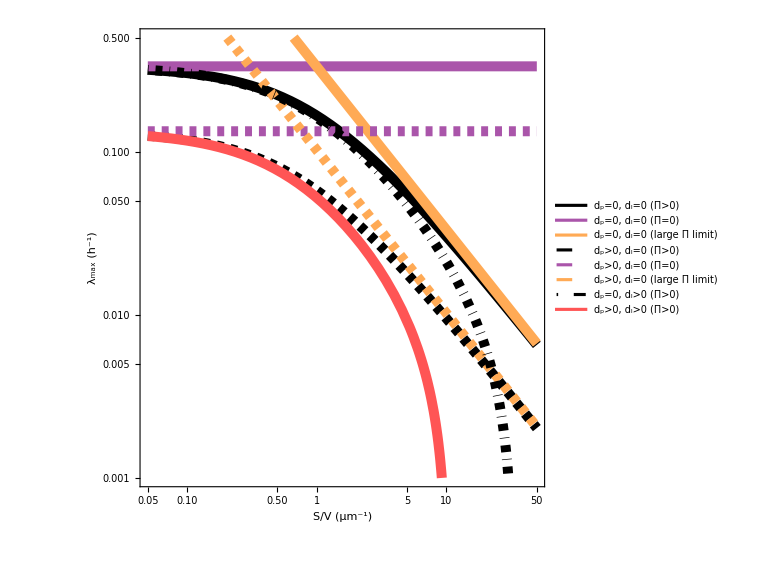

```mathematica
Plot[{
growthFull/.{κl->1,κt->1,κn->0.5,ϵ->1,dl->0,dp->0},
growthFull/.{κl->1,κt->1,κn->0.5,ϵ->1,dl->0,dp->0,Π->0},
growthFullApprox/.{κl->1,κt->1,κn->0.5,ϵ->1,dl->0,dp->0},
growthFull/.{κl->1,κt->1,κn->0.5,ϵ->1,dl->0,dp->0.3},
growthFull/.{κl->1,κt->1,κn->0.5,ϵ->1,dl->0,dp->0.3,Π->0},
growthFullApprox/.{κl->1,κt->1,κn->0.5,ϵ->1,dl->0,dp->0.3},
growthFull/.{κl->1,κt->1,κn->0.5,ϵ->1,dl->0.01,dp->0},
growthFull/.{κl->1,κt->1,κn->0.5,ϵ->1,dl->0.01,dp->0.3}
},{Π,0.05,50},Frame->True,PlotTheme->"Scientific",FrameLabel->{"S/V (μm^-1)","λ_max (h^-1)"},ImageSize->Large,PlotStyle->{
Directive[Black,Thickness[0.0125]],
Directive[Lighter[Purple],Thickness[0.0125]],
Directive[Lighter[Orange],Thickness[0.0125]],
Directive[Black,Thickness[0.0125],Dashed],
Directive[Lighter[Purple],Thickness[0.0125],Dashed],
Directive[Lighter[Orange],Thickness[0.0125],Dashed],
Directive[Black,Thickness[0.0125],DotDashed],
Directive[Lighter[Red],Thickness[0.0125]]
},ScalingFunctions->{"Log10","Log10"},FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},
PlotLegends->{"d_p=0, d_l=0 (Π>0)","d_p=0, d_l=0 (Π=0)","d_p=0, d_l=0 (large Π limit)","d_p>0, d_l=0 (Π>0)","d_p>0, d_l=0 (Π=0)","d_p>0, d_l=0 (large Π limit)","d_p=0, d_l>0 (Π>0)","d_p>0, d_l>0 (Π>0)"},PlotRange->{0.001,0.5}]
```

```mathematica
asymptNoDeg=plotStadium[-10,10,-10,10,0.03,0.5,1,1,1,1,4,4];
asymptProtDeg=plotStadium[-10,10,-10,10,0.03,0.4,1,1,1,1,4,4];
limitScale=plotStadium[-10,10,-10,10,0.2,0.4,1,1,1,1,4,4];
ultimateLimit=plotStadium[-10,10,-10,10,0.5,0,1,1,1,1,4,4];
GraphicsColumn[{asymptNoDeg,asymptProtDeg,limitScale,ultimateLimit},ImageSize->Large];
```

### Derivation of the growth laws

```mathematica
fracB=Assuming[cond,(lp*pbSolInt)/(lp*pbSolInt+lp*plSolInt+lr*rSolInt)//FullSimplify]
fracL=Assuming[cond,(lp*plSolInt)/(lp*pbSolInt+lp*plSolInt+lr*rSolInt)//FullSimplify]
fracR=Assuming[cond,(lr*rSolInt)/(lp*pbSolInt+lp*plSolInt+lr*rSolInt)//FullSimplify]
```

(λ ϕb)/(λ+dp ϕr)

(λ ϕl)/(λ+dp ϕr)

((dp+λ) ϕr)/(λ+dp ϕr)

```mathematica
κnSub=(Solve[λ==satGrowth,κn]//FullSimplify)[[1]]
fracR/.{ϕl->phiLOpt,ϕr->phiROpt}/.κnSub//FullSimplify
fracL/.{ϕl->phiLOpt,ϕr->phiROpt}/.κnSub//FullSimplify
```

{κn→(κl κt (dp+λ)+ϵ κl (dp+κt) (dl+λ) Π)/(κl (κt-λ)-ϵ (dp+κt) (dl+λ) Π)}

(dp+λ)/(dp+κt)

(ϵ (dl+λ) Π)/κl

```mathematica
CoefficientList[(ϵ (dl+λ) Π)/κl,λ]
```

{(dl ϵ Π)/κl,(ϵ Π)/κl}

```mathematica
Solve[{(dl ϵ Π)/κl==a,(ϵ Π)/κl==b},{κl,dl}]
```

{{κl→(ϵ Π)/b,dl→a/b}}

```mathematica
Solve[(ϵ Π)/κl==b,κl]//FullSimplify
```

{{κl→(ϵ Π)/b}}

```mathematica
Solve[κl==(ϵ Π)/b,b]
```

{{b→(ϵ Π)/κl}}

```mathematica
Πsub=a1-a2 λn;
```

```mathematica
ϕL==ϕLm+(ϵ Πsub)/κl λn//Expand
```

ϕL==(a1 ϵ λn)/κl-(a2 ϵ λn^2)/κl+ϕLm

```mathematica
κtSub=(Solve[λ==satGrowth,κt]//FullSimplify)[[1]]
fracR/.{ϕl->phiLOpt,ϕr->phiROpt}/.κtSub//FullSimplify
fracL/.{ϕl->phiLOpt,ϕr->phiROpt}/.κtSub//FullSimplify
```

{κt→-(κl κn λ+dp ϵ (κl+κn) (dl+λ) Π)/(κl (dp-κn+λ)+ϵ (κl+κn) (dl+λ) Π)}

(κl (dp-κn+λ)+ϵ (κl+κn) (dl+λ) Π)/(κl (dp-κn))

(ϵ (dl+λ) Π)/κl

```mathematica
CoefficientList[(κl (dp-κn+λ)+ϵ (κl+κn) (dl+λ) Π)/(κl (dp-κn)),λ]//FullSimplify
```

{1+(dl ϵ (κl+κn) Π)/(κl (dp-κn)),(κl+ϵ (κl+κn) Π)/(κl (dp-κn))}

```mathematica
Solve[{(κl+ϵ (κl+κn) Π)/(κl (dp-κn))==b},κn]//FullSimplify
```

{{κn→(κl (-1+b dp-ϵ Π))/(b κl+ϵ Π)}}

```mathematica
κlSub=(Solve[λ==satGrowth,κl]//FullSimplify)[[1]]
fracR/.{ϕl->phiLOpt,ϕr->phiROpt}/.κlSub//FullSimplify
fracL/.{ϕl->phiLOpt,ϕr->phiROpt}/.κlSub//FullSimplify
```

{κl→-(ϵ κn (dp+κt) (dl+λ) Π)/(dp κt-κn κt+κn λ+κt λ+ϵ (dp+κt) (dl+λ) Π)}

(dp+λ)/(dp+κt)

-(dp κt-κn κt+κn λ+κt λ+ϵ (dp+κt) (dl+λ) Π)/(κn (dp+κt))

```mathematica
CoefficientList[-(dp κt-κn κt+κn λ+κt λ+ϵ (dp+κt) (dl+λ) Π)/(κn (dp+κt)),λ]//FullSimplify
```

{((-dp+κn) κt-dl ϵ (dp+κt) Π)/(κn (dp+κt)),-(κn+κt+ϵ (dp+κt) Π)/(κn (dp+κt))}

### Accounting for S/V variation across growth conditions

```mathematica
CoefficientList[fracL/.{ϕl->phiLOpt,ϕr->phiROpt}/.κnSub,λ]//FullSimplify
CoefficientList[fracR/.{ϕl->phiLOpt,ϕr->phiROpt}/.κtSub,λ]//FullSimplify
```

{(dl ϵ Π)/κl,(ϵ Π)/κl}

{1+(dl ϵ (κl+κn) Π)/(κl (dp-κn)),(κl+ϵ (κl+κn) Π)/(κl (dp-κn))}

This is the envelope producer mass fraction as a function of growth rate, when the latter is modulated by changing nutrient quality

```mathematica
eqPhiL=yint+(ϵ λ Π)/κl/.{Π->a+b λ}
```

yint+(ϵ λ (a+b λ))/κl

```mathematica
volkmerPars={a->4.647,b->-0.934};
basanPars={a->5.84,b->-1.387};
siPars={a->10.14,b->-3.298};
```

```mathematica
eqPhiL/.volkmerPars
eqPhiL/.basanPars
eqPhiL/.siPars
```

yint+(ϵ (4.647-0.934 λ) λ)/κl

yint+(ϵ (5.84-1.387 λ) λ)/κl

yint+(ϵ (10.14-3.298 λ) λ)/κl

```mathematica
CoefficientList[eqPhiL/.siPars,λ]
```

{yint,(10.14 ϵ)/κl,-(3.298 ϵ)/κl}

## Comparison of numerical and analytical growth laws

```mathematica
Collect[(ϵ (dl+λ) Π)/κl/.Π->10.140-3.298λ//Expand,λ]
```

(10.14 dl ϵ)/κl+((10.14 ϵ)/κl-(3.298 dl ϵ)/κl) λ-(3.298 ϵ λ^2)/κl

```mathematica
(10.14 ϵ)/κl-(3.298 dl ϵ)/κl//FullSimplify
```

((10.14-3.298 dl) ϵ)/κl

```mathematica
piArray={
6.818,
6.19,
7.162-0.944x,
4.907,
4.838,
7.128+1.862x,
8.7,
8.22,
4.156};
```

```mathematica
1+(dl ϵ (κl+κn) Π)/(κl (dp-κn))+(κl+ϵ (κl+κn) Π)/(κl (dp-κn))x/.{dp->"dp_est",κl->"kappaL_est",κn->kN,κt->kT,ϵ->epsPar}/.Π->piArray//MatrixForm
```

(1+(6.818 dl epsPar (kappaL_est+kN))/(kappaL_est (dp_est-kN))+((kappaL_est+6.818 epsPar (kappaL_est+kN)) x)/(kappaL_est (dp_est-kN))
1+(6.19 dl epsPar (kappaL_est+kN))/(kappaL_est (dp_est-kN))+((kappaL_est+6.19 epsPar (kappaL_est+kN)) x)/(kappaL_est (dp_est-kN))
1+(dl epsPar (kappaL_est+kN) (7.162-0.944 x))/(kappaL_est (dp_est-kN))+((kappaL_est+epsPar (kappaL_est+kN) (7.162-0.944 x)) x)/(kappaL_est (dp_est-kN))
1+(4.907 dl epsPar (kappaL_est+kN))/(kappaL_est (dp_est-kN))+((kappaL_est+4.907 epsPar (kappaL_est+kN)) x)/(kappaL_est (dp_est-kN))
1+(4.838 dl epsPar (kappaL_est+kN))/(kappaL_est (dp_est-kN))+((kappaL_est+4.838 epsPar (kappaL_est+kN)) x)/(kappaL_est (dp_est-kN))
1+(dl epsPar (kappaL_est+kN) (7.128+1.862 x))/(kappaL_est (dp_est-kN))+(x (kappaL_est+epsPar (kappaL_est+kN) (7.128+1.862 x)))/(kappaL_est (dp_est-kN))
1+(8.7 dl epsPar (kappaL_est+kN))/(kappaL_est (dp_est-kN))+((kappaL_est+8.7 epsPar (kappaL_est+kN)) x)/(kappaL_est (dp_est-kN))
1+(8.22 dl epsPar (kappaL_est+kN))/(kappaL_est (dp_est-kN))+((kappaL_est+8.22 epsPar (kappaL_est+kN)) x)/(kappaL_est (dp_est-kN))
1+(4.156 dl epsPar (kappaL_est+kN))/(kappaL_est (dp_est-kN))+((kappaL_est+4.156 epsPar (kappaL_est+kN)) x)/(kappaL_est (dp_est-kN)))

### Plotting functions

Perturbation of growth via envelope synthesis inhibition:

```mathematica
pertLphiR[λ_,κn_,κl_,κt_,dp_,dl_,ϵ_,Π_]=(dp+λ)/(dp+κt);
pertLphiL[λ_,κn_,κl_,κt_,dp_,dl_,ϵ_,Π_]=-(dp κt-κn κt+κn λ+κt λ+ϵ (dp+κt) (dl+λ) Π)/(κn (dp+κt));
pertLphiB[λ_,κn_,κl_,κt_,dp_,dl_,ϵ_,Π_]=1-pertLphiR[λ,κn,κl,κt,dp,dl,ϵ,Π]-pertLphiL[λ,κn,κl,κt,dp,dl,ϵ,Π];
```

Perturbation of growth via protein synthesis inhibition:

```mathematica
pertTphiR[λ_,κn_,κl_,κt_,dp_,dl_,ϵ_,Π_]=(κl (dp-κn+λ)+ϵ (κl+κn) (dl+λ) Π)/(κl (dp-κn));
pertTphiL[λ_,κn_,κl_,κt_,dp_,dl_,ϵ_,Π_]=(ϵ (dl+λ) Π)/κl;
pertTphiB[λ_,κn_,κl_,κt_,dp_,dl_,ϵ_,Π_]=1-pertTphiR[λ,κn,κl,κt,dp,dl,ϵ,Π]-pertTphiL[λ,κn,κl,κt,dp,dl,ϵ,Π];
```

Perturbation of growth via nutrient processing inhibition:

```mathematica
pertNphiL[λ_,κn_,κl_,κt_,dp_,dl_,ϵ_,Π_]=(ϵ (dl+λ) Π)/κl;
pertNphiR[λ_,κn_,κl_,κt_,dp_,dl_,ϵ_,Π_]=(dp+λ)/(dp+κt);
pertNphiB[λ_,κn_,κl_,κt_,dp_,dl_,ϵ_,Π_]=1-pertNphiR[λ,κn,κl,κt,dp,dl,ϵ,Π]-pertNphiL[λ,κn,κl,κt,dp,dl,ϵ,Π];
```

### Perturbation of cell envelope synthesis

```mathematica
frameTicksArray={{{#,Superscript[10,Log10@#]}&/@Table[10^i,{i,-2,1}],Automatic},{{#,Superscript[10,Log10@#]}&/@Table[10^i,{i,-2,5}],Automatic}};
```

```mathematica
cellGeometryConstraint=explicitSurf/explicitVol==3/sphereRadius[explicitVol];
```

However, there is an upper limit on how many P molecs because they reside in the membrane

```mathematica
aaPerVol=325*3*10^6 (* μm^3 -- Milo and Phillips 2016 *);
lipPerSurf=2*10^6 (* μm^2 -- Langmuir 1917, Phillips 2019 *);
```

```mathematica
κlPar=0.2*288.1596;
κtPar=2.589108;
kmPar=10^-3;
dpPar=0.1438542;
dlPar=0.147;
lrPar=7336;
lpPar=325;
vDiv=10^9;
```

```mathematica
κnEmpirical={1.52728,3.228333,4.4852,6.281437,7.933559,12.144675};
κlArray=0.2*Table[i,{i,50,300,50}];
maxGrowthArray1=Table[Table[{0,0,0,0},{i,1,Length[κlArray]}],{k,1,Length[κnEmpirical]}];
violationArray1=Table[Table[{0,0},{i,1,Length[κlArray]}],{k,1,Length[κnEmpirical]}];
```

We are first interested in how proteome sectors scale with growth rate when the latter is perturbed either via κ_n or κ_l:

```mathematica
params={γ->aaPerVol,β->lipPerSurf,lp->325,lr->7336,ls->314,κt->κtPar,Km->kmPar,dp->dpPar,dl->dlPar,v->aaPerVol};
Monitor[
Do[
Do[
mainSys={ssLambda,cellGeometryConstraint}/.params/.{κl->κlArray[[i]],κn->κnEmpirical[[k]]};

numSys={mainSys[[1]],{mainSys[[2]],ϕr+ϕl+ϕb==1,1≥ϕr≥0,1≥ϕl≥0,1≥ϕb≥0}};
numSol=NOptimize[numSys,10];

maxGrowthArray1[[k,i,1]]=numSol[[2]][[All,2]][[1]] (* Subscript[ϕ, l,opt] *);
maxGrowthArray1[[k,i,2]]=numSol[[2]][[All,2]][[2]] (* Subscript[ϕ, b,opt] *);
maxGrowthArray1[[k,i,3]]=numSol[[2]][[All,2]][[3]] (* Subscript[ϕ, r,opt] *);
maxGrowthArray1[[k,i,4]]=numSol[[1]] (* λ *);

violationArray1[[k,i,1]]=numSol[[1]] (* λ *);
violationArray1[[k,i,2]]=(explicitSurf/explicitVol)/(3/sphereRadius[explicitVol])/.params/.{κl->κlArray[[i]],κn->κnEmpirical[[k]]}/.{ϕl->numSol[[2]][[All,2]][[1]],ϕb->numSol[[2]][[All,2]][[2]],ϕr->numSol[[2]][[All,2]][[3]]};
,
{i,Length[κlArray]}];,
{k,Length[κnEmpirical]}],
{k,i,κlArray[[i]],κnEmpirical[[k]]}]
```

Next, we plot both numerics and analytics for comparison:

```mathematica
plotArrayR=Table[Table[{0,0},{i,1,Length[κlArray]}],{k,1,Length[κnEmpirical]}];
xRange={0.0,1.0};
```

```mathematica
Do[
plotArrayR[[i,k,1]]=maxGrowthArray1[[i,k,4]];
plotArrayR[[i,k,2]]=((dp+λ) ϕr)/(λ+dp ϕr)/.params/.λ->maxGrowthArray1[[i,k,4]]/.ϕr->maxGrowthArray1[[i,k,3]];,
{i,1,Length[κnEmpirical]},{k,1,Length[κlArray]}]
```

```mathematica
legend={"κ_n=1.5 h^-1","κ_n=3.2 h^-1","κ_n=4.5 h^-1","κ_n=6.3 h^-1","κ_n=7.9 h^-1","κ_n=12.1 h^-1"};
```

```mathematica
(* Ribosomal mass fraction as the function of Subscript[λ, N] *)
numericRpertN=ListPlot[plotArrayR,Frame->True,PlotTheme->"Scientific",FrameLabel->{"Growth rate, λ̃ (h^-1)","Proteome mass fraction, Φ"},Joined->False,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},PlotStyle->Directive[{PointSize[0.025]}],PlotRange->{All,xRange},PlotLegends->False];
```

```mathematica
analyticR=Plot[{
pertLphiR[λ,κn,κl,κtPar,dpPar,dl,ϵ,Π]
},{λ,0.0,1.5},Frame->True,PlotTheme->"Scientific",FrameLabel->{"Growth rate, λ̃ (h^-1)","Proteome mass fraction, Φ"},ImageSize->Medium,PlotStyle->{Thickness[0.0075],Black},FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},PlotRange->{All,xRange},PlotLegends->False];
```

```mathematica
plotArrayL=Table[Table[{0,0},{i,1,Length[κlArray]}],{k,1,Length[κnEmpirical]}];
```

```mathematica
Do[
plotArrayL[[i,k,1]]=maxGrowthArray1[[i,k,4]];
plotArrayL[[i,k,2]]=(λ ϕl)/(λ+dp ϕr)/.params/.λ->maxGrowthArray1[[i,k,4]]/.{ϕl->maxGrowthArray1[[i,k,1]],ϕr->maxGrowthArray1[[i,k,3]]};,
{i,1,Length[κnEmpirical]},{k,1,Length[κlArray]}]
```

```mathematica
analyticLpertL=Plot[{
pertLphiL[λ,κnEmpirical[[1]],κl,κtPar,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]],
pertLphiL[λ,κnEmpirical[[2]],κl,κtPar,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]],
pertLphiL[λ,κnEmpirical[[3]],κl,κtPar,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]],
pertLphiL[λ,κnEmpirical[[4]],κl,κtPar,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]],
pertLphiL[λ,κnEmpirical[[5]],κl,κtPar,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]],
pertLphiL[λ,κnEmpirical[[6]],κl,κtPar,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]]
},{λ,0.0,1.5},Frame->True,PlotTheme->"Scientific",FrameLabel->{"Growth rate, λ̃ (h^-1)","Proteome mass fraction, Φ"},PlotLegends->False,ImageSize->Medium,PlotStyle->Directive[{Thickness[0.0075],Dashed}],FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},PlotRange->{All,xRange},PlotLegends->False];
```

```mathematica
(* numerics when both Subscript[κ, n] or Subscript[κ, l] are perturbed *)
numericLpertLN=ListPlot[plotArrayL,Frame->True,PlotTheme->"Scientific",Joined->False,ImageSize->Medium,FrameLabel->{"Growth rate, λ̃ (h^-1)","Proteome mass fraction, Φ"},FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},PlotStyle->Directive[{PointSize[0.025]}],PlotRange->{All,xRange},PlotMarkers->Graphics[{Thick,Circle[]},ImageSize->10],PlotLegends->False];
```

```mathematica
(* analytic for Subscript[Φ, L] when Subscript[κ, n] is perturbed *)
analyticLpertN=Plot[{
pertNphiL[λ,κn,κlArray[[1]],κt,dp,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]]
},{λ,0.0,1.5},Frame->True,PlotTheme->"Scientific",FrameLabel->{"Growth rate, λ̃ (h^-1)","Proteome mass fraction, Φ"},ImageSize->Medium,PlotStyle->{
Directive[{Black,Thickness[0.0075],DotDashed}]
},FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},PlotRange->{All,xRange},PlotLegends->False];
```

```mathematica
plotArrayB=Table[Table[{0,0},{i,1,Length[κlArray]}],{k,1,Length[κnEmpirical]}];
```

```mathematica
Do[
plotArrayB[[i,k,1]]=maxGrowthArray1[[i,k,4]];
plotArrayB[[i,k,2]]=(λ ϕb)/(λ+dp ϕr)/.params/.λ->maxGrowthArray1[[i,k,4]]/.{ϕb->maxGrowthArray1[[i,k,2]],ϕr->maxGrowthArray1[[i,k,3]]};,
{i,1,Length[κnEmpirical]},{k,1,Length[κlArray]}]
```

```mathematica
analyticBpertL=Plot[{
pertLphiB[λ,κnEmpirical[[1]],κl,κtPar,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]],
pertLphiB[λ,κnEmpirical[[2]],κl,κtPar,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]],
pertLphiB[λ,κnEmpirical[[3]],κl,κtPar,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]],
pertLphiB[λ,κnEmpirical[[4]],κl,κtPar,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]],
pertLphiB[λ,κnEmpirical[[5]],κl,κtPar,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]],
pertLphiB[λ,κnEmpirical[[6]],κl,κtPar,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]]
},{λ,0.0,1.5},Frame->True,PlotTheme->"Scientific",FrameLabel->{"Growth rate, λ̃ (h^-1)","Proteome mass fraction, Φ"},ImageSize->Medium,PlotStyle->Thickness[0.0075],FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},PlotRange->{All,xRange},PlotLegends->False];
```

```mathematica
(* numerics when both Subscript[κ, n] or Subscript[κ, l] are perturbed *)
numericBpertLN=ListPlot[plotArrayB,Frame->True,PlotTheme->"Scientific",Joined->False,ImageSize->Medium,FrameLabel->{"Growth rate, λ̃ (h^-1)","Proteome mass fraction, Φ"},FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},PlotStyle->Directive[{PointSize[0.025]}],PlotRange->{All,xRange},PlotMarkers->{"♢",15},PlotLegends->False];
```

```mathematica
(* analytic for Subscript[Φ, L] when Subscript[κ, n] is perturbed *)
analyticBpertN=Plot[{
pertNphiB[λ,κn,κlArray[[1]],κtPar,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]]
},{λ,0.0,1.5},Frame->True,PlotTheme->"Scientific",FrameLabel->{"Growth rate, (λ̃)_max (h^-1)","Proteome mass fraction, Φ"},ImageSize->Medium,PlotStyle->{
Directive[{Black,Thickness[0.0075],Dashed}]
},FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},PlotRange->{All,xRange},PlotLegends->False];
```

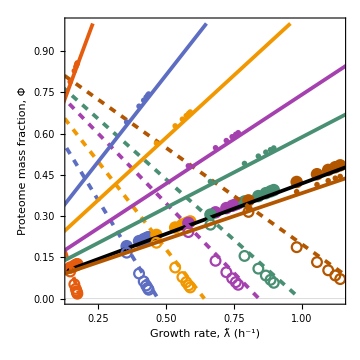

```mathematica
Show[numericRpertN,analyticR,numericLpertLN,analyticLpertL,numericBpertLN,analyticBpertL]
```

### Perturbation of protein synthesis

```mathematica
κtArray={2.589108,0.75*2.589108,0.50*2.589108};
maxGrowthArray2=Table[Table[{0,0,0,0},{i,1,Length[κtArray]}],{k,1,Length[κnEmpirical]}];
violationArray2=Table[Table[{0,0},{i,1,Length[κtArray]}],{k,1,Length[κnEmpirical]}];
```

```mathematica
params={γ->aaPerVol,β->lipPerSurf,lp->325,lr->7336,ls->314,κl->κlPar,Km->kmPar,dp->dpPar,dl->dlPar,v->aaPerVol};
Monitor[
Do[
Do[
mainSys={ssLambda,cellGeometryConstraint}/.params/.{κt->κtArray[[i]],κn->κnEmpirical[[k]]};

numSys={mainSys[[1]],{mainSys[[2]],ϕr+ϕl+ϕb==1,1≥ϕr≥0,1≥ϕl≥0,1≥ϕb≥0}};
numSol=NOptimize[numSys,10];

maxGrowthArray2[[k,i,1]]=numSol[[2]][[All,2]][[1]] (* Subscript[ϕ, l,opt] *);
maxGrowthArray2[[k,i,2]]=numSol[[2]][[All,2]][[2]] (* Subscript[ϕ, b,opt] *);
maxGrowthArray2[[k,i,3]]=numSol[[2]][[All,2]][[3]] (* Subscript[ϕ, r,opt] *);
maxGrowthArray2[[k,i,4]]=numSol[[1]] (* λ *);

violationArray2[[k,i,1]]=numSol[[1]] (* λ *);
violationArray2[[k,i,2]]=(explicitSurf/explicitVol)/(3/sphereRadius[explicitVol])/.params/.{κt->κtArray[[i]],κn->κnEmpirical[[k]]}/.{ϕl->numSol[[2]][[All,2]][[1]],ϕb->numSol[[2]][[All,2]][[2]],ϕr->numSol[[2]][[All,2]][[3]]};
,
{i,Length[κtArray]}];,
{k,Length[κnEmpirical]}],
{k,i,κtArray[[i]],κnEmpirical[[k]]}]
```

Next, we plot both numerics and analytics for comparison:

```mathematica
plotArrayR=Table[Table[{0,0},{i,1,Length[κtArray]}],{k,1,Length[κnEmpirical]}];
xRange={0.0,1.0};
```

```mathematica
Do[
plotArrayR[[i,k,1]]=maxGrowthArray2[[i,k,4]];
plotArrayR[[i,k,2]]=((dp+λ) ϕr)/(λ+dp ϕr)/.params/.λ->maxGrowthArray2[[i,k,4]]/.ϕr->maxGrowthArray2[[i,k,3]];,
{i,1,Length[κnEmpirical]},{k,1,Length[κtArray]}]
```

```mathematica
legend={"κ_n=1.5 h^-1","κ_n=3.2 h^-1","κ_n=4.5 h^-1","κ_n=6.3 h^-1","κ_n=7.9 h^-1","κ_n=12.1 h^-1"};
```

```mathematica
(* Ribosomal mass fraction as the function of Subscript[λ, N] *)
numericRpertN=ListPlot[plotArrayR,Frame->True,PlotTheme->"Scientific",FrameLabel->{"Growth rate, λ̃ (h^-1)","Proteome mass fraction, Φ"},Joined->False,ImageSize->Medium,FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},PlotStyle->Directive[{PointSize[0.025]}],PlotRange->{All,xRange},PlotLegends->False];
```

```mathematica
analyticR=Plot[{
pertTphiR[λ,κnEmpirical[[1]],κlPar,κt,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]],
pertTphiR[λ,κnEmpirical[[2]],κlPar,κt,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]],
pertTphiR[λ,κnEmpirical[[3]],κlPar,κt,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]],
pertTphiR[λ,κnEmpirical[[4]],κlPar,κt,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]],
pertTphiR[λ,κnEmpirical[[5]],κlPar,κt,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]],
pertTphiR[λ,κnEmpirical[[6]],κlPar,κt,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]]
},{λ,0.0,1.5},Frame->True,PlotTheme->"Scientific",FrameLabel->{"Growth rate, λ̃ (h^-1)","Proteome mass fraction, Φ"},ImageSize->Medium,PlotStyle->{Thickness[0.0075],Automatic},FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},PlotRange->{All,xRange},PlotLegends->False];
```

```mathematica
plotArrayL=Table[Table[{0,0},{i,1,Length[κtArray]}],{k,1,Length[κnEmpirical]}];
```

```mathematica
Do[
plotArrayL[[i,k,1]]=maxGrowthArray2[[i,k,4]];
plotArrayL[[i,k,2]]=(λ ϕl)/(λ+dp ϕr)/.params/.λ->maxGrowthArray2[[i,k,4]]/.{ϕl->maxGrowthArray2[[i,k,1]],ϕr->maxGrowthArray2[[i,k,3]]};,
{i,1,Length[κnEmpirical]},{k,1,Length[κtArray]}]
```

```mathematica
analyticLpertT=Plot[{
pertTphiL[λ,κn,κlPar,κt,dp,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]]
},{λ,0.0,1.5},Frame->True,PlotTheme->"Scientific",FrameLabel->{"Growth rate, λ̃ (h^-1)","Proteome mass fraction, Φ"},PlotLegends->False,ImageSize->Medium,PlotStyle->Directive[Thickness[0.0075],Black],FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},PlotRange->{All,All},PlotLegends->False];
```

```mathematica
(* numerics when both Subscript[κ, n] or Subscript[κ, l] are perturbed *)
numericLpertTN=ListPlot[plotArrayL,Frame->True,PlotTheme->"Scientific",Joined->False,ImageSize->Medium,FrameLabel->{"Growth rate, λ̃ (h^-1)","Proteome mass fraction, Φ"},FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},PlotStyle->Directive[{PointSize[0.025]}],PlotRange->{All,All},PlotMarkers->Graphics[{Thick,Circle[]},ImageSize->10],PlotLegends->False];
```

```mathematica
plotArrayB=Table[Table[{0,0},{i,1,Length[κtArray]}],{k,1,Length[κnEmpirical]}];
```

```mathematica
Do[
plotArrayB[[i,k,1]]=maxGrowthArray2[[i,k,4]];
plotArrayB[[i,k,2]]=(λ ϕb)/(λ+dp ϕr)/.params/.λ->maxGrowthArray2[[i,k,4]]/.{ϕb->maxGrowthArray2[[i,k,2]],ϕr->maxGrowthArray2[[i,k,3]]};,
{i,1,Length[κnEmpirical]},{k,1,Length[κtArray]}]
```

```mathematica
analyticBpertT=Plot[{
pertTphiB[λ,κnEmpirical[[1]],κlPar,κt,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]],
pertTphiB[λ,κnEmpirical[[2]],κlPar,κt,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]],
pertTphiB[λ,κnEmpirical[[3]],κlPar,κt,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]],
pertTphiB[λ,κnEmpirical[[4]],κlPar,κt,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]],
pertTphiB[λ,κnEmpirical[[5]],κlPar,κt,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]],
pertTphiB[λ,κnEmpirical[[6]],κlPar,κt,dpPar,dlPar,lipPerSurf/aaPerVol*314,3/sphereRadius[1]]
},{λ,0.0,1.5},Frame->True,PlotTheme->"Scientific",FrameLabel->{"Growth rate, λ̃ (h^-1)","Proteome mass fraction, Φ"},ImageSize->Medium,PlotStyle->Directive[Thickness[0.0075],Dashed],FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},PlotRange->{All,xRange},PlotLegends->False];
```

```mathematica
(* numerics when both Subscript[κ, n] or Subscript[κ, l] are perturbed *)
numericBpertTN=ListPlot[plotArrayB,Frame->True,PlotTheme->"Scientific",Joined->False,ImageSize->Medium,FrameLabel->{"Growth rate, (λ̃)_max (h^-1)","Proteome mass fraction, Φ"},FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},PlotStyle->Directive[{PointSize[0.025]}],PlotRange->{All,xRange},PlotMarkers->{"♢",15},PlotLegends->False];
```

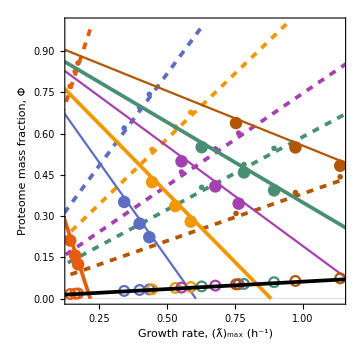

```mathematica
Show[numericBpertTN,analyticBpertT,numericRpertN,analyticR,numericLpertTN,analyticLpertT]
```

```mathematica
loNutloEnvInhib=plotStadium[-10,10,-10,10,0.2,0.3,1,1,1,1,4,4];
loNuthiEnvInhib=plotStadium[-10,10,-10,10,0.3,0.25,1,1,1,1,4,4];
hiNutloEnvInhib=plotStadium[-10,10,-10,10,0.25,0.5,1,1,1,1,4,4];
hiNuthiEnvInhib=plotStadium[-10,10,-10,10,0.3,0.4,1,1,1,1,4,4];
```

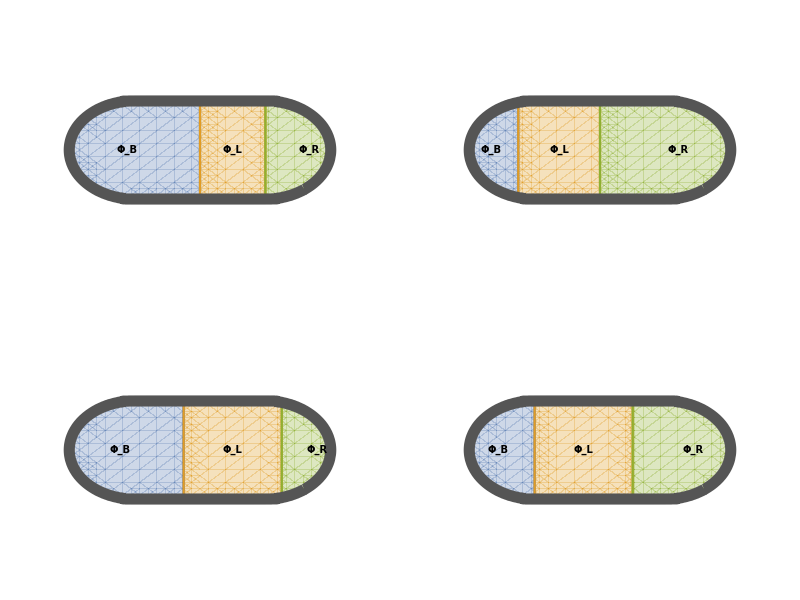

```mathematica
Grid[{{loNutloEnvInhib,hiNutloEnvInhib},{loNuthiEnvInhib,hiNuthiEnvInhib}}]
```

```mathematica
loNutloTrlInhib=plotStadium[-10,10,-10,10,0.2,0.3,1,1,1,1,4,4];
loNuthiTrlInhib=plotStadium[-10,10,-10,10,0.10,0.5,1,1,1,1,4,4];
hiNutloTrlInhib=plotStadium[-10,10,-10,10,0.25,0.5,1,1,1,1,4,4];
hiNuthiTrlInhib=plotStadium[-10,10,-10,10,0.15,0.65,1,1,1,1,4,4];
```

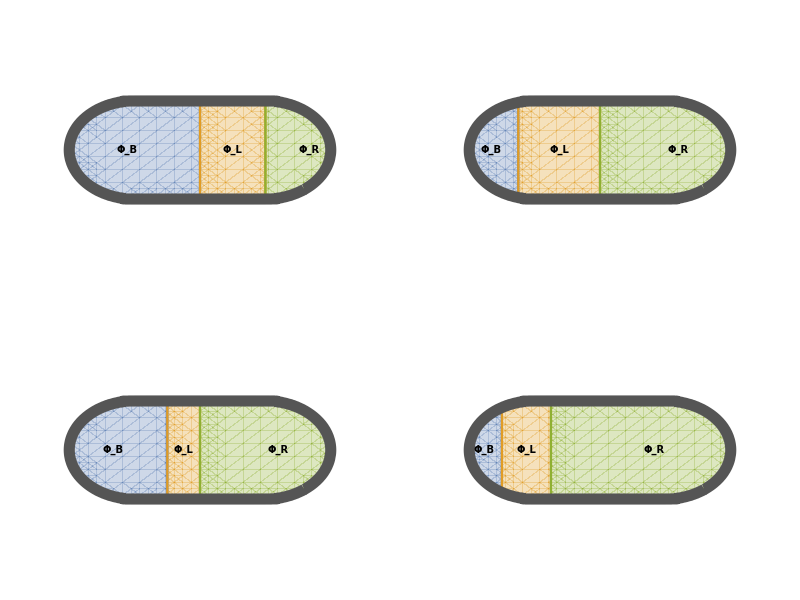

```mathematica
Grid[{{loNutloTrlInhib,hiNutloTrlInhib},{loNuthiTrlInhib,hiNuthiTrlInhib}}]
```

## Deriving correction for anaerobic metabolism

```mathematica
knCorrection[gr_]=Flatten[Solve[(10^6*x*325)/10^9==gr,x]//N][[All,2]][[1]]
```

3.07692 gr

```mathematica
knCorrection[0.46]
knCorrection[0.73]
```

1.41538

2.24615

```mathematica
xx=((κn-dp) κt)/(κn+κt)*1/(1+(ϵ (κl+κn) (dp+κt) (dl κn+(dl-dp+κn) κt) Π)/((κn+κt) (κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π)))/.κn->κn*α
```

((-dp+α κn) κt)/((α κn+κt) (1+(ϵ (κl+α κn) (dp+κt) (dl α κn+(dl-dp+α κn) κt) Π)/((α κn+κt) (κl (-dp+α κn) κt-dl ϵ (κl+α κn) (dp+κt) Π))))

```mathematica
Solve[((κn-dp) κt)/(κn+κt)*1/(1+(ϵ (κl+κn) (dp+κt) (dl κn+(dl-dp+κn) κt) Π)/((κn+κt) (κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π)))==y*xx,y]//FullSimplify
```

{{y→((κl (dp-κn) κt+dl ϵ (κl+κn) (dp+κt) Π) (κl (α κn+κt)+ϵ (κl+α κn) (dp+κt) Π))/((κl (κn+κt)+ϵ (κl+κn) (dp+κt) Π) (κl (dp-α κn) κt+dl ϵ (κl+α κn) (dp+κt) Π))}}

## Error propagation

```mathematica
D[temp(1-dp*b)/b,b]^2*VarB//FullSimplify (* std. for Subscript[κ, t] estimate *)
D[temp(ϵ Π)/b,b]^2*VarB//FullSimplify (* std. for Subscript[κ, l] estimate, if estimated via OLS *)
D[temp*kl,kl]^2*VarKl (* std. for Subscript[κ, l] estimate, if estimated via NLS *)
```

(temp^2 VarB)/b^4

(temp^2 VarB ϵ^2 Π^2)/b^4

temp^2 VarKl

```mathematica
D[temp(κl (-1+b dp-ϵ Π))/(b κl+ϵ Π),b]^2*VarB+D[temp(κl (-1+b dp-ϵ Π))/(b κl+ϵ Π),κl]^2*VarKl//FullSimplify (* std. for Subscript[κ, n] estimate *)
```

(temp^2 (VarKl ϵ^2 Π^2 (1-b dp+ϵ Π)^2+VarB κl^2 (κl+ϵ (dp+κl) Π)^2))/(b κl+ϵ Π)^4

```mathematica
Collect[(temp^2 (VarKl ϵ^2 Π^2 (1-b dp+ϵ Π)^2+VarB κl^2 (κl+ϵ (dp+κl) Π)^2))/(b κl+ϵ Π)^4,{VarB,VarKl}]
```

(temp^2 VarKl ϵ^2 Π^2 (1-b dp+ϵ Π)^2)/(b κl+ϵ Π)^4+(temp^2 VarB κl^2 (κl+ϵ (dp+κl) Π)^2)/(b κl+ϵ Π)^4

## Scaling of metabolic rate with S/V

```mathematica
pbSolExp
plSolExp
rSolExp
lSolExp
```

-(κt ϕb ϕr V[t])/(lp (dp-κn) ϕb+lp (dp+κl) ϕl)

-(κt ϕl ϕr V[t])/(lp (dp-κn) ϕb+lp (dp+κl) ϕl)

-(ϕr (dp+κt ϕr) V[t])/(lr (dp-κn) ϕb+lr (dp+κl) ϕl)

-(κl κt ϕl ϕr V[t])/(ls (-κn ϕb+κl ϕl+dp (ϕb+ϕl)) (dl+κt ϕr))

```mathematica
Solve[Π==2π V^(2/3-1),V]
```

{{V→(8 π^3)/Π^3}}

```mathematica
phiROpt
phiLOpt
```

(κl (-dp+κn) κt-dl ϵ (κl+κn) (dp+κt) Π)/(κl κt (κn+κt)+ϵ (κl+κn) κt (dp+κt) Π)

(ϵ (dp+κt) (dl κn+(dl-dp+κn) κt) Π)/(κl κt (κn+κt)+ϵ (κl+κn) κt (dp+κt) Π)

```mathematica
mrEq=((Qaa lp κn Pb[t]+Ql lp κl/ls Pl[t]+Qt lr κt R[t]+Qdp dp (Pb[t]+Pl[t])+Qdl dl L[t])/.{Pb[t]->pbSolExp,Pl[t]->plSolExp,R[t]->rSolExp,L[t]->lSolExp}/.ϕb->1-ϕr-ϕl);
```

```mathematica
mrSpecOpt=mrEq/(V[t]/γ)/.{ϕr->phiROpt,ϕl->phiLOpt}//FullSimplify
```

1/(lp ls (κl (κn+κt)+ϵ (κl+κn) (dp+κt) Π))γ (ls κl (dp Qdp+lp (Qaa+Qt) κn) κt+ϵ ((dp (ls Qdp-lp Ql+lp ls Qt) κl+dp ls (Qdp+lp (Qaa+Qt)) κn+lp (ls Qaa+Ql) κl κn) κt+dl (lp (ls Qaa+Qdl+Ql) κl κn+dp ls Qdp (κl+κn)+lp ((Qdl+Ql-ls Qt) κl-ls (Qaa+Qt) κn) κt)) Π+dl lp Qdl ϵ^2 (κl+κn) (dp+κt) Π^2)

```mathematica
mrSpecOpt/.{Π->svPar,ϵ->epsPar,κn->kN,κt->kT,κl->kL}//FullSimplify
```

1/(lp ls (kL (kN+kT)+epsPar (kL+kN) (dp+kT) svPar))(kL kT ls (dp Qdp+kN lp (Qaa+Qt))+epsPar (kT (kL kN lp (ls Qaa+Ql)+dp kN ls (Qdp+lp (Qaa+Qt))+dp kL (-lp Ql+ls (Qdp+lp Qt)))+dl (dp (kL+kN) ls Qdp+kL kN lp (ls Qaa+Qdl+Ql)+kT lp (-kN ls (Qaa+Qt)+kL (Qdl+Ql-ls Qt)))) svPar+dl epsPar^2 (kL+kN) (dp+kT) lp Qdl svPar^2) γ

```mathematica
compFactor=mrSpecOpt/satGrowth/.{dl->0,dp->0}//FullSimplify
rateFactor=satGrowth/.{dl->0,dp->0}//FullSimplify
compFactor*rateFactor==mrSpecOpt/.{dl->0,dp->0}//FullSimplify
```

γ (Qaa+Qt+Qaa ϵ Π+(Ql ϵ Π)/ls)

(κl κn κt)/(κl (κn+κt)+ϵ (κl+κn) κt Π)

True

```mathematica
mrSpecOpt/.{dl->0,dp->0}//FullSimplify
```

(γ κl κn κt (Ql ϵ Π+ls (Qaa+Qt+Qaa ϵ Π)))/(ls κl (κn+κt)+ls ϵ (κl+κn) κt Π)

```mathematica
Solve[D[mrSpecOpt/.{dl->0,dp->0},Π]==0,ls]/.{κl->k,κn->k,κt->k}//FullSimplify
```

{{ls→Ql/Qt}}

```mathematica
Reduce[(D[mrSpecOpt/.{dl->0,dp->0},Π]//FullSimplify)>0&&κn>0&&κt>0&&κl>0&&ϵ>0&&Π>0&&Ql>0&&Qt>0&&ls>0&&Qt>0&&γ>0]//FullSimplify
```

Qaa∈ℝ&&κt>0&&κn>0&&Ql>0&&Qt>0&&γ>0&&ϵ>0&&Π>0&&ls>0&&((κl==κt&&ls<(Ql κl (κn+κt))/(Qt (κl+κn) κt))||(κl>0&&Qaa<(ls Qt (κl+κn) κt-Ql κl (κn+κt))/(ls κn (κl-κt))&&κl<κt)||(Qaa>(ls Qt (κl+κn) κt-Ql κl (κn+κt))/(ls κn (κl-κt))&&κl>κt))

```mathematica
Solve[(D[mrSpecOpt/.{dl->0,dp->0},Π]==0//FullSimplify),ls]//FullSimplify
```

{{ls→(Ql κl (κn+κt))/(Qt (κl+κn) κt+Qaa κn (-κl+κt))}}

```mathematica
(* 
cx -- Costs (direct + missed synthesis opportunity) associated with process x;
caa -- The cost of producing an amino acid;
ct -- The cost of adding an amino acid to a growing polypeptide chain;
cl -- The costs of producing one unit of cell envelope;
cdp -- The costs of degrading an average protein = Mean[{0.25,1}] ATP × 325 aa/protein [from Lynch and Marinov 2015];
cdl -- The costs of degrading a unit of cell envelope = Assumed to be zero, because cell wall hydrolases seem to be ATP-independent;
*)
```

```mathematica
aaDirCost=2+2*Mean[{1,3,1,1,4,1,1,0,-2,5,1,4,8,2,3,0,3,1,1,2}]
lppPerAACost=4+aaDirCost
```

6

10

E. coli cell has roughly 4.32μm^2/cell (Prats and Pedro 1989), and three layers are lipids. This is because the outer leaflet of the outer membrane is composed of LPS molecules:

```mathematica
lipPerSurf=(22*10^6/3)/4.32
```

1.69753×10^6

```mathematica
pgnPerSurf=(3.5*10^6)/4.32
```

810185.

```mathematica
lpsPerSurf=1.43*10^6/4.32
```

331019.

```mathematica
aaPerSurf=78*10^6/4.32
```

1.80556×10^7

```mathematica
lipPerUnit=lipPerSurf/lipPerSurf
pgnPerUnit=pgnPerSurf/lipPerSurf
lpsPerUnit=lpsPerSurf/lipPerSurf
aaPerUnit=aaPerSurf/lipPerSurf
```

1.

0.477273

0.195

10.6364

```mathematica
qlPar=74*3*lipPerUnit+17*pgnPerUnit+301*lpsPerUnit+lppPerAACost*aaPerUnit
```

395.172

```mathematica
lpsPar=((27+4)*aaPerUnit+223*pgnPerUnit+271*3*lipPerUnit+2243*lpsPerUnit)/27
```

62.4646

```mathematica
qPars={Qaa->aaDirCost,Qt->4,Ql->qlPar,Qdp->1*325,Qdl->0};
```

```mathematica
parsMR={κt->2.6,κl->27.75,dp->0.011,dl->0.211,ϵ->0.11,lp->325,lr->7336,ls->lpsPar,γ->(0.24*10^-12*6.022*10^23)/110,α->10^0.83,β->0.659-1};
```

```mathematica
atpE=47*1000/(6.022*10^23);
```

```mathematica
kappaNarray={0.476,0.979,1.34,1.84,2.285,3.36};
```

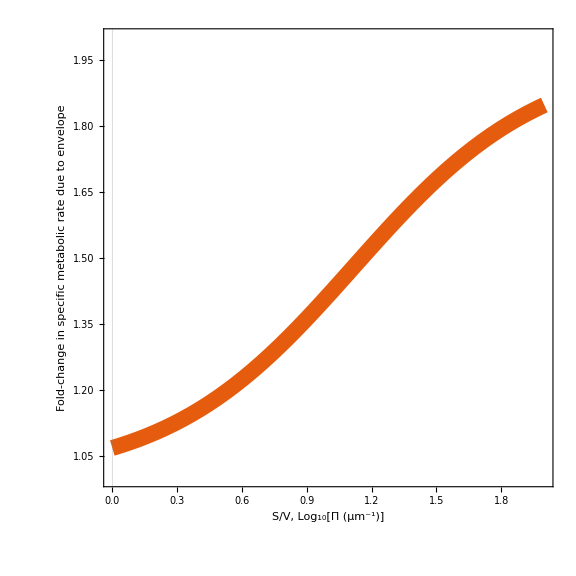

```mathematica
Plot[{
(atpE*mrSpecOpt)/(atpE*mrSpecOpt/.ϵ->0)/.Π->10^x/.parsMR/.κn->kappaNarray[[3]]/.qPars
},{x,0,2},Frame->True,PlotTheme->"Scientific",FrameLabel->{"S/V, Log_10[Π (μm^-1)]","Fold-change in specific metabolic rate due to envelope"},ImageSize->Large,FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],AspectRatio->1,LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},PlotStyle->Directive[{Thickness[0.02]}],PlotRange->{All,{1,2}}]
```

```mathematica
mrSpecOpt/.{dp->0,dl->0,ϵ->0}//FullSimplify
Limit[mrSpecOpt/.{dp->0,dl->0},Π->Infinity]//FullSimplify
Limit[mrSpecOpt/.{dp->0,dl->0},Π->0]//FullSimplify
```

((Qaa+Qt) γ κn κt)/(κn+κt)

((ls Qaa+Ql) γ κl κn)/(ls (κl+κn))

((Qaa+Qt) γ κn κt)/(κn+κt)

```mathematica
Assuming[κn>0&&κt>0&&κl>0&&ϵ>0&&Π>0&&Ql>0&&Qt>0&&ls>0&&Qt>0&&γ>0&&Qaa>0&&Ql>0,Limit[compFactor,Π->Infinity]//Simplify]
Assuming[κn>0&&κt>0&&κl>0&&ϵ>0&&Π>0&&Ql>0&&Qt>0&&ls>0&&Qt>0&&γ>0&&Qaa>0&&Ql>0,Limit[rateFactor,Π->Infinity]//Simplify]
Assuming[κn>0&&κt>0&&κl>0&&ϵ>0&&Π>0&&Ql>0&&Qt>0&&ls>0&&Qt>0&&γ>0&&Qaa>0&&Ql>0,Limit[compFactor*rateFactor,Π->Infinity]//Simplify]
```

∞

0

((ls Qaa+Ql) γ κl κn)/(ls (κl+κn))

```mathematica
Series[rateFactor,{Π,Infinity,1}]
```

(κl κn)/(ϵ (κl+κn) Π)+O[1/Π]^2